```mathematica
(* WALKING KINEMATICS: Segment angles and polar co-ordinates - Filtered, Archive data*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(*This code use the data outputs from WALKING KINEMATICS: Segment angles and polar co-ordinates.nb. This code looks at all trials simultaneously*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Determine operating system *)

os=$OperatingSystem;
frogworkpath="C:\\YOUR FILE DIRECTORY HERE\\" (*Set your main file directory, not to the folder where raw or archived data are stored*)
(*e.g. frogworkpath="C:\\Users\\Documents\\"*)
(*for Mac users change "C:\\" to "\\Volumes\\"*)


(***********************************************************************************)

(* Import metadata*)
(*Set the directory where the METADATA.xlsx is saved*)

(*SET DIRECTORY*)
dataDirectory="YOUR DIRECTORY TO METADATA.xlsx FILE";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

importedmetadata=Import["METADATA.xlsx","Data"];
metadata=importedmetadata[[1,2;;24,All]];

(***********************************************************************************)

(* Metadata file map: Locate information *)

Framerate=metadata[[3,1]];
```

```mathematica
(******************************************************************************************)

(* Import the polar co-ordinate data files created with Semgnet Angles - Polar Coords - Version 3.nb  *)

(*Set directory*)
dataDirectory="YOUR DIRECTORY FOR EXPORTED POLOR COORDINATES";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*Import data*)

(*Femur*)
(*Vertical*)
Animal0Trial1FEMVdata=Flatten[Import["KM01_RUN_02_FemurVertical.xlsx","Data"]];
Animal1Trial1FEMVdata=Flatten[Import["KM02_RUN_01_FemurVertical.xlsx","Data"]];
Animal1Trial2FEMVdata=Flatten[Import["KM02_RUN_02_FemurVertical.xlsx","Data"]];
Animal1Trial3FEMVdata=Flatten[Import["KM02_RUN_09_FemurVertical.xlsx","Data"]];
Animal2Trial1FEMVdata=Flatten[Import["KM04_RUN_09_FemurVertical.xlsx","Data"]];
Animal2Trial2FEMVdata=Flatten[Import["KM04_RUN_11_FemurVertical.xlsx","Data"]];
Animal2Trial3FEMVdata=Flatten[Import["KM04_RUN_12_FemurVertical.xlsx","Data"]];
Animal3Trial1FEMVdata=Flatten[Import["KM05_RUN_04_FemurVertical.xlsx","Data"]];
Animal3Trial2FEMVdata=Flatten[Import["KM05_RUN_08_FemurVertical.xlsx","Data"]];
Animal4Trial1FEMVdata=Flatten[Import["KM06_RUN_11_FemurVertical.xlsx","Data"]];
Animal4Trial2FEMVdata=Flatten[Import["KM06_RUN_12_FemurVertical.xlsx","Data"]];
Animal4Trial3FEMVdata=Flatten[Import["KM06_RUN_13_FemurVertical.xlsx","Data"]];
Animal4Trial4FEMVdata=Flatten[Import["KM06_RUN_15_FemurVertical.xlsx","Data"]];
Animal4Trial5FEMVdata=Flatten[Import["KM06_RUN_16_FemurVertical.xlsx","Data"]];
Animal5Trial1FEMVdata=Flatten[Import["KM07_RUN_14_FemurVertical.xlsx","Data"]];
Animal5Trial2FEMVdata=Flatten[Import["KM07_RUN_16_FemurVertical.xlsx","Data"]];
Animal5Trial3FEMVdata=Flatten[Import["KM07_RUN_17_FemurVertical.xlsx","Data"]];
Animal6Trial1FEMVdata=Flatten[Import["KM08_RUN_09_FemurVertical.xlsx","Data"]];
Animal6Trial2FEMVdata=Flatten[Import["KM08_RUN_10_FemurVertical.xlsx","Data"]];
Animal7Trial1FEMVdata=Flatten[Import["KM23_RUN_01_FemurVertical.xlsx","Data"]];
Animal7Trial2FEMVdata=Flatten[Import["KM23_RUN_02_FemurVertical.xlsx","Data"]];Animal7Trial3FEMVdata=Flatten[Import["KM23_RUN_03_FemurVertical.xlsx","Data"]];
Animal7Trial4FEMVdata=Flatten[Import["KM23_RUN_05_FemurVertical.xlsx","Data"]];

(*Horizontal*)
Animal0Trial1FEMHdata=Flatten[Import["KM01_RUN_02_FemurHorizontal.xlsx","Data"]];
Animal1Trial1FEMHdata=Flatten[Import["KM02_RUN_01_FemurHorizontal.xlsx","Data"]];
Animal1Trial2FEMHdata=Flatten[Import["KM02_RUN_02_FemurHorizontal.xlsx","Data"]];
Animal1Trial3FEMHdata=Flatten[Import["KM02_RUN_09_FemurHorizontal.xlsx","Data"]];
Animal2Trial1FEMHdata=Flatten[Import["KM04_RUN_09_FemurHorizontal.xlsx","Data"]];
Animal2Trial2FEMHdata=Flatten[Import["KM04_RUN_11_FemurHorizontal.xlsx","Data"]];
Animal2Trial3FEMHdata=Flatten[Import["KM04_RUN_12_FemurHorizontal.xlsx","Data"]];
Animal3Trial1FEMHdata=Flatten[Import["KM05_RUN_04_FemurHorizontal.xlsx","Data"]];
Animal3Trial2FEMHdata=Flatten[Import["KM05_RUN_08_FemurHorizontal.xlsx","Data"]];
Animal4Trial1FEMHdata=Flatten[Import["KM06_RUN_11_FemurHorizontal.xlsx","Data"]];
Animal4Trial2FEMHdata=Flatten[Import["KM06_RUN_12_FemurHorizontal.xlsx","Data"]];
Animal4Trial3FEMHdata=Flatten[Import["KM06_RUN_13_FemurHorizontal.xlsx","Data"]];
Animal4Trial4FEMHdata=Flatten[Import["KM06_RUN_15_FemurHorizontal.xlsx","Data"]];
Animal4Trial5FEMHdata=Flatten[Import["KM06_RUN_16_FemurHorizontal.xlsx","Data"]];
Animal5Trial1FEMHdata=Flatten[Import["KM07_RUN_14_FemurHorizontal.xlsx","Data"]];
Animal5Trial2FEMHdata=Flatten[Import["KM07_RUN_16_FemurHorizontal.xlsx","Data"]];
Animal5Trial3FEMHdata=Flatten[Import["KM07_RUN_17_FemurHorizontal.xlsx","Data"]];
Animal6Trial1FEMHdata=Flatten[Import["KM08_RUN_09_FemurHorizontal.xlsx","Data"]];
Animal6Trial2FEMHdata=Flatten[Import["KM08_RUN_10_FemurHorizontal.xlsx","Data"]];
Animal7Trial1FEMHdata=Flatten[Import["KM23_RUN_01_FemurHorizontal.xlsx","Data"]];
Animal7Trial2FEMHdata=Flatten[Import["KM23_RUN_02_FemurHorizontal.xlsx","Data"]];Animal7Trial3FEMHdata=Flatten[Import["KM23_RUN_03_FemurHorizontal.xlsx","Data"]];
Animal7Trial4FEMHdata=Flatten[Import["KM23_RUN_05_FemurHorizontal.xlsx","Data"]];

(*TibFib*)
(*Vertical*)
Animal0Trial1TIBVdata=Flatten[Import["KM01_RUN_02_TibfibVertical.xlsx","Data"]];
Animal1Trial1TIBVdata=Flatten[Import["KM02_RUN_01_TibfibVertical.xlsx","Data"]];
Animal1Trial2TIBVdata=Flatten[Import["KM02_RUN_02_TibfibVertical.xlsx","Data"]];
Animal1Trial3TIBVdata=Flatten[Import["KM02_RUN_09_TibfibVertical.xlsx","Data"]];
Animal2Trial1TIBVdata=Flatten[Import["KM04_RUN_09_TibfibVertical.xlsx","Data"]];
Animal2Trial2TIBVdata=Flatten[Import["KM04_RUN_11_TibfibVertical.xlsx","Data"]];
Animal2Trial3TIBVdata=Flatten[Import["KM04_RUN_12_TibfibVertical.xlsx","Data"]];
Animal3Trial1TIBVdata=Flatten[Import["KM05_RUN_04_TibfibVertical.xlsx","Data"]];
Animal3Trial2TIBVdata=Flatten[Import["KM05_RUN_08_TibfibVertical.xlsx","Data"]];
Animal4Trial1TIBVdata=Flatten[Import["KM06_RUN_11_TibfibVertical.xlsx","Data"]];
Animal4Trial2TIBVdata=Flatten[Import["KM06_RUN_12_TibfibVertical.xlsx","Data"]];
Animal4Trial3TIBVdata=Flatten[Import["KM06_RUN_13_TibfibVertical.xlsx","Data"]];
Animal4Trial4TIBVdata=Flatten[Import["KM06_RUN_15_TibfibVertical.xlsx","Data"]];
Animal4Trial5TIBVdata=Flatten[Import["KM06_RUN_16_TibfibVertical.xlsx","Data"]];
Animal5Trial1TIBVdata=Flatten[Import["KM07_RUN_14_TibfibVertical.xlsx","Data"]];
Animal5Trial2TIBVdata=Flatten[Import["KM07_RUN_16_TibfibVertical.xlsx","Data"]];
Animal5Trial3TIBVdata=Flatten[Import["KM07_RUN_17_TibfibVertical.xlsx","Data"]];
Animal6Trial1TIBVdata=Flatten[Import["KM08_RUN_09_TibfibVertical.xlsx","Data"]];
Animal6Trial2TIBVdata=Flatten[Import["KM08_RUN_10_TibfibVertical.xlsx","Data"]];
Animal7Trial1TIBVdata=Flatten[Import["KM23_RUN_01_TibfibVertical.xlsx","Data"]];
Animal7Trial2TIBVdata=Flatten[Import["KM23_RUN_02_TibfibVertical.xlsx","Data"]];Animal7Trial3TIBVdata=Flatten[Import["KM23_RUN_03_TibfibVertical.xlsx","Data"]];
Animal7Trial4TIBVdata=Flatten[Import["KM23_RUN_05_TibfibVertical.xlsx","Data"]];

(*Horizontal*)
Animal0Trial1TIBHdata=Flatten[Import["KM01_RUN_02_TibfibHorizontal.xlsx","Data"]];
Animal1Trial1TIBHdata=Flatten[Import["KM02_RUN_01_TibfibHorizontal.xlsx","Data"]];
Animal1Trial2TIBHdata=Flatten[Import["KM02_RUN_02_TibfibHorizontal.xlsx","Data"]];
Animal1Trial3TIBHdata=Flatten[Import["KM02_RUN_09_TibfibHorizontal.xlsx","Data"]];
Animal2Trial1TIBHdata=Flatten[Import["KM04_RUN_09_TibfibHorizontal.xlsx","Data"]];
Animal2Trial2TIBHdata=Flatten[Import["KM04_RUN_11_TibfibHorizontal.xlsx","Data"]];
Animal2Trial3TIBHdata=Flatten[Import["KM04_RUN_12_TibfibHorizontal.xlsx","Data"]];
Animal3Trial1TIBHdata=Flatten[Import["KM05_RUN_04_TibfibHorizontal.xlsx","Data"]];
Animal3Trial2TIBHdata=Flatten[Import["KM05_RUN_08_TibfibHorizontal.xlsx","Data"]];
Animal4Trial1TIBHdata=Flatten[Import["KM06_RUN_11_TibfibHorizontal.xlsx","Data"]];
Animal4Trial2TIBHdata=Flatten[Import["KM06_RUN_12_TibfibHorizontal.xlsx","Data"]];
Animal4Trial3TIBHdata=Flatten[Import["KM06_RUN_13_TibfibHorizontal.xlsx","Data"]];
Animal4Trial4TIBHdata=Flatten[Import["KM06_RUN_15_TibfibHorizontal.xlsx","Data"]];
Animal4Trial5TIBHdata=Flatten[Import["KM06_RUN_16_TibfibHorizontal.xlsx","Data"]];
Animal5Trial1TIBHdata=Flatten[Import["KM07_RUN_14_TibfibHorizontal.xlsx","Data"]];
Animal5Trial2TIBHdata=Flatten[Import["KM07_RUN_16_TibfibHorizontal.xlsx","Data"]];
Animal5Trial3TIBHdata=Flatten[Import["KM07_RUN_17_TibfibHorizontal.xlsx","Data"]];
Animal6Trial1TIBHdata=Flatten[Import["KM08_RUN_09_TibfibHorizontal.xlsx","Data"]];
Animal6Trial2TIBHdata=Flatten[Import["KM08_RUN_10_TibfibHorizontal.xlsx","Data"]];
Animal7Trial1TIBHdata=Flatten[Import["KM23_RUN_01_TibfibHorizontal.xlsx","Data"]];
Animal7Trial2TIBHdata=Flatten[Import["KM23_RUN_02_TibfibHorizontal.xlsx","Data"]];Animal7Trial3TIBHdata=Flatten[Import["KM23_RUN_03_TibfibHorizontal.xlsx","Data"]];
Animal7Trial4TIBHdata=Flatten[Import["KM23_RUN_05_TibfibHorizontal.xlsx","Data"]];

(*Tarsals*)
(*Vertical*)
Animal0Trial1TARVdata=Flatten[Import["KM01_RUN_02_TarsalsVertical.xlsx","Data"]];
Animal1Trial1TARVdata=Flatten[Import["KM02_RUN_01_TarsalsVertical.xlsx","Data"]];
Animal1Trial2TARVdata=Flatten[Import["KM02_RUN_02_TarsalsVertical.xlsx","Data"]];
Animal1Trial3TARVdata=Flatten[Import["KM02_RUN_09_TarsalsVertical.xlsx","Data"]];
Animal2Trial1TARVdata=Flatten[Import["KM04_RUN_09_TarsalsVertical.xlsx","Data"]];
Animal2Trial2TARVdata=Flatten[Import["KM04_RUN_11_TarsalsVertical.xlsx","Data"]];
Animal2Trial3TARVdata=Flatten[Import["KM04_RUN_12_TarsalsVertical.xlsx","Data"]];
Animal3Trial1TARVdata=Flatten[Import["KM05_RUN_04_TarsalsVertical.xlsx","Data"]];
Animal3Trial2TARVdata=Flatten[Import["KM05_RUN_08_TarsalsVertical.xlsx","Data"]];
Animal4Trial1TARVdata=Flatten[Import["KM06_RUN_11_TarsalsVertical.xlsx","Data"]];
Animal4Trial2TARVdata=Flatten[Import["KM06_RUN_12_TarsalsVertical.xlsx","Data"]];
Animal4Trial3TARVdata=Flatten[Import["KM06_RUN_13_TarsalsVertical.xlsx","Data"]];
Animal4Trial4TARVdata=Flatten[Import["KM06_RUN_15_TarsalsVertical.xlsx","Data"]];
Animal4Trial5TARVdata=Flatten[Import["KM06_RUN_16_TarsalsVertical.xlsx","Data"]];
Animal5Trial1TARVdata=Flatten[Import["KM07_RUN_14_TarsalsVertical.xlsx","Data"]];
Animal5Trial2TARVdata=Flatten[Import["KM07_RUN_16_TarsalsVertical.xlsx","Data"]];
Animal5Trial3TARVdata=Flatten[Import["KM07_RUN_17_TarsalsVertical.xlsx","Data"]];
Animal6Trial1TARVdata=Flatten[Import["KM08_RUN_09_TarsalsVertical.xlsx","Data"]];
Animal6Trial2TARVdata=Flatten[Import["KM08_RUN_10_TarsalsVertical.xlsx","Data"]];
Animal7Trial1TARVdata=Flatten[Import["KM23_RUN_01_TarsalsVertical.xlsx","Data"]];
Animal7Trial2TARVdata=Flatten[Import["KM23_RUN_02_TarsalsVertical.xlsx","Data"]];Animal7Trial3TARVdata=Flatten[Import["KM23_RUN_03_TarsalsVertical.xlsx","Data"]];
Animal7Trial4TARVdata=Flatten[Import["KM23_RUN_05_TarsalsVertical.xlsx","Data"]];

(*Horizontal*)
Animal0Trial1TARHdata=Flatten[Import["KM01_RUN_02_TarsalsHorizontal.xlsx","Data"]];
Animal1Trial1TARHdata=Flatten[Import["KM02_RUN_01_TarsalsHorizontal.xlsx","Data"]];
Animal1Trial2TARHdata=Flatten[Import["KM02_RUN_02_TarsalsHorizontal.xlsx","Data"]];
Animal1Trial3TARHdata=Flatten[Import["KM02_RUN_09_TarsalsHorizontal.xlsx","Data"]];
Animal2Trial1TARHdata=Flatten[Import["KM04_RUN_09_TarsalsHorizontal.xlsx","Data"]];
Animal2Trial2TARHdata=Flatten[Import["KM04_RUN_11_TarsalsHorizontal.xlsx","Data"]];
Animal2Trial3TARHdata=Flatten[Import["KM04_RUN_12_TarsalsHorizontal.xlsx","Data"]];
Animal3Trial1TARHdata=Flatten[Import["KM05_RUN_04_TarsalsHorizontal.xlsx","Data"]];
Animal3Trial2TARHdata=Flatten[Import["KM05_RUN_08_TarsalsHorizontal.xlsx","Data"]];
Animal4Trial1TARHdata=Flatten[Import["KM06_RUN_11_TarsalsHorizontal.xlsx","Data"]];
Animal4Trial2TARHdata=Flatten[Import["KM06_RUN_12_TarsalsHorizontal.xlsx","Data"]];
Animal4Trial3TARHdata=Flatten[Import["KM06_RUN_13_TarsalsHorizontal.xlsx","Data"]];
Animal4Trial4TARHdata=Flatten[Import["KM06_RUN_15_TarsalsHorizontal.xlsx","Data"]];
Animal4Trial5TARHdata=Flatten[Import["KM06_RUN_16_TarsalsHorizontal.xlsx","Data"]];
Animal5Trial1TARHdata=Flatten[Import["KM07_RUN_14_TarsalsHorizontal.xlsx","Data"]];
Animal5Trial2TARHdata=Flatten[Import["KM07_RUN_16_TarsalsHorizontal.xlsx","Data"]];
Animal5Trial3TARHdata=Flatten[Import["KM07_RUN_17_TarsalsHorizontal.xlsx","Data"]];
Animal6Trial1TARHdata=Flatten[Import["KM08_RUN_09_TarsalsHorizontal.xlsx","Data"]];
Animal6Trial2TARHdata=Flatten[Import["KM08_RUN_10_TarsalsHorizontal.xlsx","Data"]];
Animal7Trial1TARHdata=Flatten[Import["KM23_RUN_01_TarsalsHorizontal.xlsx","Data"]];
Animal7Trial2TARHdata=Flatten[Import["KM23_RUN_02_TarsalsHorizontal.xlsx","Data"]];Animal7Trial3TARHdata=Flatten[Import["KM23_RUN_03_TarsalsHorizontal.xlsx","Data"]];
Animal7Trial4TARHdata=Flatten[Import["KM23_RUN_05_TarsalsHorizontal.xlsx","Data"]];




(*************************************************************************************************************)
```

```mathematica
(*Put data in degrees*)

(*Femur*)
(*Vertical*)
Animal0Trial1FEMV=Animal0Trial1FEMVdata/Degree;
Animal1Trial1FEMV=Animal1Trial1FEMVdata/Degree;
Animal1Trial2FEMV=Animal1Trial2FEMVdata/Degree;
Animal1Trial3FEMV=Animal1Trial3FEMVdata/Degree;
Animal2Trial1FEMV=Animal2Trial1FEMVdata/Degree;
Animal2Trial2FEMV=Animal2Trial2FEMVdata/Degree;
Animal2Trial3FEMV=Animal2Trial3FEMVdata/Degree;
Animal3Trial1FEMV=Animal3Trial1FEMVdata/Degree;
Animal3Trial2FEMV=Animal3Trial2FEMVdata/Degree;
Animal4Trial1FEMV=Animal4Trial1FEMVdata/Degree;
Animal4Trial2FEMV=Animal4Trial2FEMVdata/Degree;
Animal4Trial3FEMV=Animal4Trial3FEMVdata/Degree;
Animal4Trial4FEMV=Animal4Trial4FEMVdata/Degree;
Animal4Trial5FEMV=Animal4Trial5FEMVdata/Degree;
Animal5Trial1FEMV=Animal5Trial1FEMVdata/Degree;
Animal5Trial2FEMV=Animal5Trial2FEMVdata/Degree;
Animal5Trial3FEMV=Animal5Trial3FEMVdata/Degree;
Animal6Trial1FEMV=Animal6Trial1FEMVdata/Degree;
Animal6Trial2FEMV=Animal6Trial2FEMVdata/Degree;
Animal7Trial1FEMV=Animal7Trial1FEMVdata/Degree;
Animal7Trial2FEMV=Animal7Trial2FEMVdata/Degree;
Animal7Trial3FEMV=Animal7Trial3FEMVdata/Degree;
Animal7Trial4FEMV=Animal7Trial4FEMVdata/Degree;

(*Horizontal*)
Animal0Trial1FEMH=Animal0Trial1FEMHdata/Degree;
Animal1Trial1FEMH=Animal1Trial1FEMHdata/Degree;
Animal1Trial2FEMH=Animal1Trial2FEMHdata/Degree;
Animal1Trial3FEMH=Animal1Trial3FEMHdata/Degree;
Animal2Trial1FEMH=Animal2Trial1FEMHdata/Degree;
Animal2Trial2FEMH=Animal2Trial2FEMHdata/Degree;
Animal2Trial3FEMH=Animal2Trial3FEMHdata/Degree;
Animal3Trial1FEMH=Animal3Trial1FEMHdata/Degree;
Animal3Trial2FEMH=Animal3Trial2FEMHdata/Degree;
Animal4Trial1FEMH=Animal4Trial1FEMHdata/Degree;
Animal4Trial2FEMH=Animal4Trial2FEMHdata/Degree;
Animal4Trial3FEMH=Animal4Trial3FEMHdata/Degree;
Animal4Trial4FEMH=Animal4Trial4FEMHdata/Degree;
Animal4Trial5FEMH=Animal4Trial5FEMHdata/Degree;
Animal5Trial1FEMH=Animal5Trial1FEMHdata/Degree;
Animal5Trial2FEMH=Animal5Trial2FEMHdata/Degree;
Animal5Trial3FEMH=Animal5Trial3FEMHdata/Degree;
Animal6Trial1FEMH=Animal6Trial1FEMHdata/Degree;
Animal6Trial2FEMH=Animal6Trial2FEMHdata/Degree;
Animal7Trial1FEMH=Animal7Trial1FEMHdata/Degree;
Animal7Trial2FEMH=Animal7Trial2FEMHdata/Degree;
Animal7Trial3FEMH=Animal7Trial3FEMHdata/Degree;
Animal7Trial4FEMH=Animal7Trial4FEMHdata/Degree;

(*TibFib*)
(*Vertical*)
Animal0Trial1TIBV=Animal0Trial1TIBVdata/Degree;
Animal1Trial1TIBV=Animal1Trial1TIBVdata/Degree;
Animal1Trial2TIBV=Animal1Trial2TIBVdata/Degree;
Animal1Trial3TIBV=Animal1Trial3TIBVdata/Degree;
Animal2Trial1TIBV=Animal2Trial1TIBVdata/Degree;
Animal2Trial2TIBV=Animal2Trial2TIBVdata/Degree;
Animal2Trial3TIBV=Animal2Trial3TIBVdata/Degree;
Animal3Trial1TIBV=Animal3Trial1TIBVdata/Degree;
Animal3Trial2TIBV=Animal3Trial2TIBVdata/Degree;
Animal4Trial1TIBV=Animal4Trial1TIBVdata/Degree;
Animal4Trial2TIBV=Animal4Trial2TIBVdata/Degree;
Animal4Trial3TIBV=Animal4Trial3TIBVdata/Degree;
Animal4Trial4TIBV=Animal4Trial4TIBVdata/Degree;
Animal4Trial5TIBV=Animal4Trial5TIBVdata/Degree;
Animal5Trial1TIBV=Animal5Trial1TIBVdata/Degree;
Animal5Trial2TIBV=Animal5Trial2TIBVdata/Degree;
Animal5Trial3TIBV=Animal5Trial3TIBVdata/Degree;
Animal6Trial1TIBV=Animal6Trial1TIBVdata/Degree;
Animal6Trial2TIBV=Animal6Trial2TIBVdata/Degree;
Animal7Trial1TIBV=Animal7Trial1TIBVdata/Degree;
Animal7Trial2TIBV=Animal7Trial2TIBVdata/Degree;
Animal7Trial3TIBV=Animal7Trial3TIBVdata/Degree;
Animal7Trial4TIBV=Animal7Trial4TIBVdata/Degree;

(*Horizontal*)
Animal0Trial1TIBH=Animal0Trial1TIBHdata/Degree;
Animal1Trial1TIBH=Animal1Trial1TIBHdata/Degree;
Animal1Trial2TIBH=Animal1Trial2TIBHdata/Degree;
Animal1Trial3TIBH=Animal1Trial3TIBHdata/Degree;
Animal2Trial1TIBH=Animal2Trial1TIBHdata/Degree;
Animal2Trial2TIBH=Animal2Trial2TIBHdata/Degree;
Animal2Trial3TIBH=Animal2Trial3TIBHdata/Degree;
Animal3Trial1TIBH=Animal3Trial1TIBHdata/Degree;
Animal3Trial2TIBH=Animal3Trial2TIBHdata/Degree;
Animal4Trial1TIBH=Animal4Trial1TIBHdata/Degree;
Animal4Trial2TIBH=Animal4Trial2TIBHdata/Degree;
Animal4Trial3TIBH=Animal4Trial3TIBHdata/Degree;
Animal4Trial4TIBH=Animal4Trial4TIBHdata/Degree;
Animal4Trial5TIBH=Animal4Trial5TIBHdata/Degree;
Animal5Trial1TIBH=Animal5Trial1TIBHdata/Degree;
Animal5Trial2TIBH=Animal5Trial2TIBHdata/Degree;
Animal5Trial3TIBH=Animal5Trial3TIBHdata/Degree;
Animal6Trial1TIBH=Animal6Trial1TIBHdata/Degree;
Animal6Trial2TIBH=Animal6Trial2TIBHdata/Degree;
Animal7Trial1TIBH=Animal7Trial1TIBHdata/Degree;
Animal7Trial2TIBH=Animal7Trial2TIBHdata/Degree;
Animal7Trial3TIBH=Animal7Trial3TIBHdata/Degree;
Animal7Trial4TIBH=Animal7Trial4TIBHdata/Degree;

(*Tarsals*)
(*Vertical*)
Animal0Trial1TARV=Animal0Trial1TARVdata/Degree;
Animal1Trial1TARV=Animal1Trial1TARVdata/Degree;
Animal1Trial2TARV=Animal1Trial2TARVdata/Degree;
Animal1Trial3TARV=Animal1Trial3TARVdata/Degree;
Animal2Trial1TARV=Animal2Trial1TARVdata/Degree;
Animal2Trial2TARV=Animal2Trial2TARVdata/Degree;
Animal2Trial3TARV=Animal2Trial3TARVdata/Degree;
Animal3Trial1TARV=Animal3Trial1TARVdata/Degree;
Animal3Trial2TARV=Animal3Trial2TARVdata/Degree;
Animal4Trial1TARV=Animal4Trial1TARVdata/Degree;
Animal4Trial2TARV=Animal4Trial2TARVdata/Degree;
Animal4Trial3TARV=Animal4Trial3TARVdata/Degree;
Animal4Trial4TARV=Animal4Trial4TARVdata/Degree;
Animal4Trial5TARV=Animal4Trial5TARVdata/Degree;
Animal5Trial1TARV=Animal5Trial1TARVdata/Degree;
Animal5Trial2TARV=Animal5Trial2TARVdata/Degree;
Animal5Trial3TARV=Animal5Trial3TARVdata/Degree;
Animal6Trial1TARV=Animal6Trial1TARVdata/Degree;
Animal6Trial2TARV=Animal6Trial2TARVdata/Degree;
Animal7Trial1TARV=Animal7Trial1TARVdata/Degree;
Animal7Trial2TARV=Animal7Trial2TARVdata/Degree;
Animal7Trial3TARV=Animal7Trial3TARVdata/Degree;
Animal7Trial4TARV=Animal7Trial4TARVdata/Degree;

(*Horizontal*)
Animal0Trial1TARH=Animal0Trial1TARHdata/Degree;
Animal1Trial1TARH=Animal1Trial1TARHdata/Degree;
Animal1Trial2TARH=Animal1Trial2TARHdata/Degree;
Animal1Trial3TARH=Animal1Trial3TARHdata/Degree;
Animal2Trial1TARH=Animal2Trial1TARHdata/Degree;
Animal2Trial2TARH=Animal2Trial2TARHdata/Degree;
Animal2Trial3TARH=Animal2Trial3TARHdata/Degree;
Animal3Trial1TARH=Animal3Trial1TARHdata/Degree;
Animal3Trial2TARH=Animal3Trial2TARHdata/Degree;
Animal4Trial1TARH=Animal4Trial1TARHdata/Degree;
Animal4Trial2TARH=Animal4Trial2TARHdata/Degree;
Animal4Trial3TARH=Animal4Trial3TARHdata/Degree;
Animal4Trial4TARH=Animal4Trial4TARHdata/Degree;
Animal4Trial5TARH=Animal4Trial5TARHdata/Degree;
Animal5Trial1TARH=Animal5Trial1TARHdata/Degree;
Animal5Trial2TARH=Animal5Trial2TARHdata/Degree;
Animal5Trial3TARH=Animal5Trial3TARHdata/Degree;
Animal6Trial1TARH=Animal6Trial1TARHdata/Degree;
Animal6Trial2TARH=Animal6Trial2TARHdata/Degree;
Animal7Trial1TARH=Animal7Trial1TARHdata/Degree;
Animal7Trial2TARH=Animal7Trial2TARHdata/Degree;
Animal7Trial3TARH=Animal7Trial3TARHdata/Degree;
Animal7Trial4TARH=Animal7Trial4TARHdata/Degree;
```

```mathematica
(*************************************************************************************************************)
```

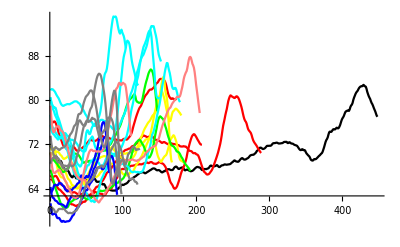

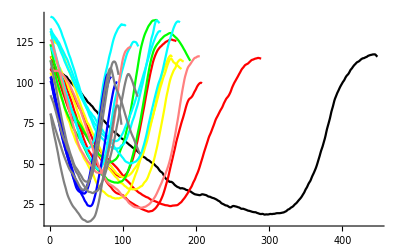

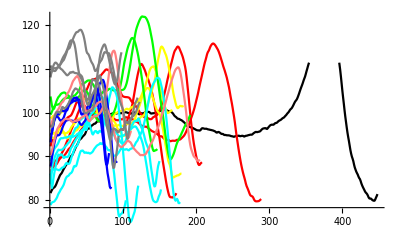

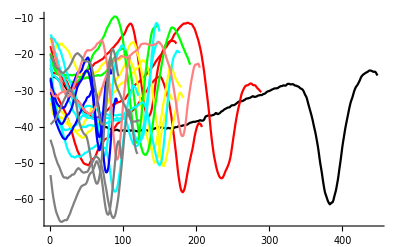

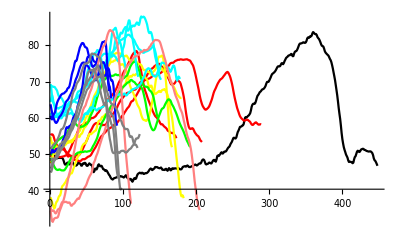

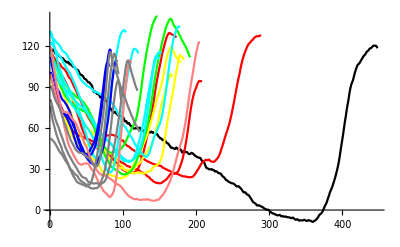

```mathematica
(* Create plots *)

(* Absolute time *)

(*Femur*)
(*Vertical*)
Animal0Trial1FEMVplot=ListLinePlot[Animal0Trial1FEMV,PlotStyle->Black];
Animal1Trial1FEMVplot=ListLinePlot[Animal1Trial1FEMV,PlotStyle->Red];
Animal1Trial2FEMVplot=ListLinePlot[Animal1Trial2FEMV,PlotStyle->Red];
Animal1Trial3FEMVplot=ListLinePlot[Animal1Trial3FEMV,PlotStyle->Red];
Animal2Trial1FEMVplot=ListLinePlot[Animal2Trial1FEMV,PlotStyle->Yellow];
Animal2Trial2FEMVplot=ListLinePlot[Animal2Trial2FEMV,PlotStyle->Yellow];
Animal2Trial3FEMVplot=ListLinePlot[Animal2Trial3FEMV,PlotStyle->Yellow];
Animal3Trial1FEMVplot=ListLinePlot[Animal3Trial1FEMV,PlotStyle->Green];
Animal3Trial2FEMVplot=ListLinePlot[Animal3Trial2FEMV,PlotStyle->Green];
Animal4Trial1FEMVplot=ListLinePlot[Animal4Trial1FEMV,PlotStyle->Cyan];
Animal4Trial2FEMVplot=ListLinePlot[Animal4Trial2FEMV,PlotStyle->Cyan];
Animal4Trial3FEMVplot=ListLinePlot[Animal4Trial3FEMV,PlotStyle->Cyan];
Animal4Trial4FEMVplot=ListLinePlot[Animal4Trial4FEMV,PlotStyle->Cyan];
Animal4Trial5FEMVplot=ListLinePlot[Animal4Trial5FEMV,PlotStyle->Cyan];
Animal5Trial1FEMVplot=ListLinePlot[Animal5Trial1FEMV,PlotStyle->Blue];
Animal5Trial2FEMVplot=ListLinePlot[Animal5Trial2FEMV,PlotStyle->Blue];
Animal5Trial3FEMVplot=ListLinePlot[Animal5Trial3FEMV,PlotStyle->Blue];
Animal6Trial1FEMVplot=ListLinePlot[Animal6Trial1FEMV,PlotStyle->Pink];
Animal6Trial2FEMVplot=ListLinePlot[Animal6Trial2FEMV,PlotStyle->Pink];
Animal7Trial1FEMVplot=ListLinePlot[Animal7Trial1FEMV,PlotStyle->Gray];
Animal7Trial2FEMVplot=ListLinePlot[Animal7Trial2FEMV,PlotStyle->Gray];
Animal7Trial3FEMVplot=ListLinePlot[Animal7Trial3FEMV,PlotStyle->Gray];
Animal7Trial4FEMVplot=ListLinePlot[Animal7Trial4FEMV,PlotStyle->Gray];

AllAnimal0FEMVplot=Show[Animal0Trial1FEMVplot];
AllAnimal1FEMVplot=Show[Animal1Trial1FEMVplot,Animal1Trial2FEMVplot,Animal1Trial3FEMVplot];
AllAnimal2FEMVplot=Show[Animal2Trial1FEMVplot,Animal2Trial2FEMVplot,Animal2Trial3FEMVplot];
AllAnimal3FEMVplot=Show[Animal3Trial1FEMVplot,Animal3Trial2FEMVplot];
AllAnimal4FEMVplot=Show[Animal4Trial1FEMVplot,Animal4Trial2FEMVplot,Animal4Trial3FEMVplot,Animal4Trial4FEMVplot,Animal4Trial5FEMVplot];
AllAnimal5FEMVplot=Show[Animal5Trial1FEMVplot,Animal5Trial2FEMVplot,Animal5Trial3FEMVplot];
AllAnimal6FEMVplot=Show[Animal6Trial1FEMVplot,Animal6Trial2FEMVplot,PlotRange->All];
AllAnimal7FEMVplot=Show[Animal7Trial1FEMVplot,Animal7Trial2FEMVplot,Animal7Trial3FEMVplot,Animal7Trial4FEMVplot];
AllAnimalsAllTrialsHip=Show[AllAnimal0FEMVplot,AllAnimal1FEMVplot,AllAnimal2FEMVplot,AllAnimal3FEMVplot,AllAnimal4FEMVplot,AllAnimal5FEMVplot,AllAnimal6FEMVplot,AllAnimal7FEMVplot,PlotRange->All]

(*Horizontal*)
Animal0Trial1FEMHplot=ListLinePlot[Animal0Trial1FEMH,PlotStyle->Black];
Animal1Trial1FEMHplot=ListLinePlot[Animal1Trial1FEMH,PlotStyle->Red];
Animal1Trial2FEMHplot=ListLinePlot[Animal1Trial2FEMH,PlotStyle->Red];
Animal1Trial3FEMHplot=ListLinePlot[Animal1Trial3FEMH,PlotStyle->Red];
Animal2Trial1FEMHplot=ListLinePlot[Animal2Trial1FEMH,PlotStyle->Yellow];
Animal2Trial2FEMHplot=ListLinePlot[Animal2Trial2FEMH,PlotStyle->Yellow];
Animal2Trial3FEMHplot=ListLinePlot[Animal2Trial3FEMH,PlotStyle->Yellow];
Animal3Trial1FEMHplot=ListLinePlot[Animal3Trial1FEMH,PlotStyle->Green];
Animal3Trial2FEMHplot=ListLinePlot[Animal3Trial2FEMH,PlotStyle->Green];
Animal4Trial1FEMHplot=ListLinePlot[Animal4Trial1FEMH,PlotStyle->Cyan];
Animal4Trial2FEMHplot=ListLinePlot[Animal4Trial2FEMH,PlotStyle->Cyan];
Animal4Trial3FEMHplot=ListLinePlot[Animal4Trial3FEMH,PlotStyle->Cyan];
Animal4Trial4FEMHplot=ListLinePlot[Animal4Trial4FEMH,PlotStyle->Cyan];
Animal4Trial5FEMHplot=ListLinePlot[Animal4Trial5FEMH,PlotStyle->Cyan];
Animal5Trial1FEMHplot=ListLinePlot[Animal5Trial1FEMH,PlotStyle->Blue];
Animal5Trial2FEMHplot=ListLinePlot[Animal5Trial2FEMH,PlotStyle->Blue];
Animal5Trial3FEMHplot=ListLinePlot[Animal5Trial3FEMH,PlotStyle->Blue];
Animal6Trial1FEMHplot=ListLinePlot[Animal6Trial1FEMH,PlotStyle->Pink];
Animal6Trial2FEMHplot=ListLinePlot[Animal6Trial2FEMH,PlotStyle->Pink];
Animal7Trial1FEMHplot=ListLinePlot[Animal7Trial1FEMH,PlotStyle->Gray];
Animal7Trial2FEMHplot=ListLinePlot[Animal7Trial2FEMH,PlotStyle->Gray];
Animal7Trial3FEMHplot=ListLinePlot[Animal7Trial3FEMH,PlotStyle->Gray];
Animal7Trial4FEMHplot=ListLinePlot[Animal7Trial4FEMH,PlotStyle->Gray];

AllAnimal0FEMHplot=Show[Animal0Trial1FEMHplot];
AllAnimal1FEMHplot=Show[Animal1Trial1FEMHplot,Animal1Trial2FEMHplot,Animal1Trial3FEMHplot];
AllAnimal2FEMHplot=Show[Animal2Trial1FEMHplot,Animal2Trial2FEMHplot,Animal2Trial3FEMHplot];
AllAnimal3FEMHplot=Show[Animal3Trial1FEMHplot,Animal3Trial2FEMHplot];
AllAnimal4FEMHplot=Show[Animal4Trial1FEMHplot,Animal4Trial2FEMHplot,Animal4Trial3FEMHplot,Animal4Trial4FEMHplot,Animal4Trial5FEMHplot];
AllAnimal5FEMHplot=Show[Animal5Trial1FEMHplot,Animal5Trial2FEMHplot,Animal5Trial3FEMHplot];
AllAnimal6FEMHplot=Show[Animal6Trial1FEMHplot,Animal6Trial2FEMHplot,PlotRange->All];
AllAnimal7FEMHplot=Show[Animal7Trial1FEMHplot,Animal7Trial2FEMHplot,Animal7Trial3FEMHplot,Animal7Trial4FEMHplot];
AllAnimalsAllTrialsHip=Show[AllAnimal0FEMHplot,AllAnimal1FEMHplot,AllAnimal2FEMHplot,AllAnimal3FEMHplot,AllAnimal4FEMHplot,AllAnimal5FEMHplot,AllAnimal6FEMHplot,AllAnimal7FEMHplot,PlotRange->All]

(*TibFib*)
(*Vertical*)
Animal0Trial1TIBVplot=ListLinePlot[Animal0Trial1TIBV,PlotStyle->Black];
Animal1Trial1TIBVplot=ListLinePlot[Animal1Trial1TIBV,PlotStyle->Red];
Animal1Trial2TIBVplot=ListLinePlot[Animal1Trial2TIBV,PlotStyle->Red];
Animal1Trial3TIBVplot=ListLinePlot[Animal1Trial3TIBV,PlotStyle->Red];
Animal2Trial1TIBVplot=ListLinePlot[Animal2Trial1TIBV,PlotStyle->Yellow];
Animal2Trial2TIBVplot=ListLinePlot[Animal2Trial2TIBV,PlotStyle->Yellow];
Animal2Trial3TIBVplot=ListLinePlot[Animal2Trial3TIBV,PlotStyle->Yellow];
Animal3Trial1TIBVplot=ListLinePlot[Animal3Trial1TIBV,PlotStyle->Green];
Animal3Trial2TIBVplot=ListLinePlot[Animal3Trial2TIBV,PlotStyle->Green];
Animal4Trial1TIBVplot=ListLinePlot[Animal4Trial1TIBV,PlotStyle->Cyan];
Animal4Trial2TIBVplot=ListLinePlot[Animal4Trial2TIBV,PlotStyle->Cyan];
Animal4Trial3TIBVplot=ListLinePlot[Animal4Trial3TIBV,PlotStyle->Cyan];
Animal4Trial4TIBVplot=ListLinePlot[Animal4Trial4TIBV,PlotStyle->Cyan];
Animal4Trial5TIBVplot=ListLinePlot[Animal4Trial5TIBV,PlotStyle->Cyan];
Animal5Trial1TIBVplot=ListLinePlot[Animal5Trial1TIBV,PlotStyle->Blue];
Animal5Trial2TIBVplot=ListLinePlot[Animal5Trial2TIBV,PlotStyle->Blue];
Animal5Trial3TIBVplot=ListLinePlot[Animal5Trial3TIBV,PlotStyle->Blue];
Animal6Trial1TIBVplot=ListLinePlot[Animal6Trial1TIBV,PlotStyle->Pink];
Animal6Trial2TIBVplot=ListLinePlot[Animal6Trial2TIBV,PlotStyle->Pink];
Animal7Trial1TIBVplot=ListLinePlot[Animal7Trial1TIBV,PlotStyle->Gray];
Animal7Trial2TIBVplot=ListLinePlot[Animal7Trial2TIBV,PlotStyle->Gray];
Animal7Trial3TIBVplot=ListLinePlot[Animal7Trial3TIBV,PlotStyle->Gray];
Animal7Trial4TIBVplot=ListLinePlot[Animal7Trial4TIBV,PlotStyle->Gray];

AllAnimal0TIBVplot=Show[Animal0Trial1TIBVplot];
AllAnimal1TIBVplot=Show[Animal1Trial1TIBVplot,Animal1Trial2TIBVplot,Animal1Trial3TIBVplot];
AllAnimal2TIBVplot=Show[Animal2Trial1TIBVplot,Animal2Trial2TIBVplot,Animal2Trial3TIBVplot];
AllAnimal3TIBVplot=Show[Animal3Trial1TIBVplot,Animal3Trial2TIBVplot];
AllAnimal4TIBVplot=Show[Animal4Trial1TIBVplot,Animal4Trial2TIBVplot,Animal4Trial3TIBVplot,Animal4Trial4TIBVplot,Animal4Trial5TIBVplot];
AllAnimal5TIBVplot=Show[Animal5Trial1TIBVplot,Animal5Trial2TIBVplot,Animal5Trial3TIBVplot];
AllAnimal6TIBVplot=Show[Animal6Trial1TIBVplot,Animal6Trial2TIBVplot,PlotRange->All];
AllAnimal7TIBVplot=Show[Animal7Trial1TIBVplot,Animal7Trial2TIBVplot,Animal7Trial3TIBVplot,Animal7Trial4TIBVplot];
AllAnimalsAllTrialsHip=Show[AllAnimal0TIBVplot,AllAnimal1TIBVplot,AllAnimal2TIBVplot,AllAnimal3TIBVplot,AllAnimal4TIBVplot,AllAnimal5TIBVplot,AllAnimal6TIBVplot,AllAnimal7TIBVplot,PlotRange->All]

(*Horizontal*)
Animal0Trial1TIBHplot=ListLinePlot[Animal0Trial1TIBH,PlotStyle->Black];
Animal1Trial1TIBHplot=ListLinePlot[Animal1Trial1TIBH,PlotStyle->Red];
Animal1Trial2TIBHplot=ListLinePlot[Animal1Trial2TIBH,PlotStyle->Red];
Animal1Trial3TIBHplot=ListLinePlot[Animal1Trial3TIBH,PlotStyle->Red];
Animal2Trial1TIBHplot=ListLinePlot[Animal2Trial1TIBH,PlotStyle->Yellow];
Animal2Trial2TIBHplot=ListLinePlot[Animal2Trial2TIBH,PlotStyle->Yellow];
Animal2Trial3TIBHplot=ListLinePlot[Animal2Trial3TIBH,PlotStyle->Yellow];
Animal3Trial1TIBHplot=ListLinePlot[Animal3Trial1TIBH,PlotStyle->Green];
Animal3Trial2TIBHplot=ListLinePlot[Animal3Trial2TIBH,PlotStyle->Green];
Animal4Trial1TIBHplot=ListLinePlot[Animal4Trial1TIBH,PlotStyle->Cyan];
Animal4Trial2TIBHplot=ListLinePlot[Animal4Trial2TIBH,PlotStyle->Cyan];
Animal4Trial3TIBHplot=ListLinePlot[Animal4Trial3TIBH,PlotStyle->Cyan];
Animal4Trial4TIBHplot=ListLinePlot[Animal4Trial4TIBH,PlotStyle->Cyan];
Animal4Trial5TIBHplot=ListLinePlot[Animal4Trial5TIBH,PlotStyle->Cyan];
Animal5Trial1TIBHplot=ListLinePlot[Animal5Trial1TIBH,PlotStyle->Blue];
Animal5Trial2TIBHplot=ListLinePlot[Animal5Trial2TIBH,PlotStyle->Blue];
Animal5Trial3TIBHplot=ListLinePlot[Animal5Trial3TIBH,PlotStyle->Blue];
Animal6Trial1TIBHplot=ListLinePlot[Animal6Trial1TIBH,PlotStyle->Pink];
Animal6Trial2TIBHplot=ListLinePlot[Animal6Trial2TIBH,PlotStyle->Pink];
Animal7Trial1TIBHplot=ListLinePlot[Animal7Trial1TIBH,PlotStyle->Gray];
Animal7Trial2TIBHplot=ListLinePlot[Animal7Trial2TIBH,PlotStyle->Gray];
Animal7Trial3TIBHplot=ListLinePlot[Animal7Trial3TIBH,PlotStyle->Gray];
Animal7Trial4TIBHplot=ListLinePlot[Animal7Trial4TIBH,PlotStyle->Gray];

AllAnimal0TIBHplot=Show[Animal0Trial1TIBHplot];
AllAnimal1TIBHplot=Show[Animal1Trial1TIBHplot,Animal1Trial2TIBHplot,Animal1Trial3TIBHplot];
AllAnimal2TIBHplot=Show[Animal2Trial1TIBHplot,Animal2Trial2TIBHplot,Animal2Trial3TIBHplot];
AllAnimal3TIBHplot=Show[Animal3Trial1TIBHplot,Animal3Trial2TIBHplot];
AllAnimal4TIBHplot=Show[Animal4Trial1TIBHplot,Animal4Trial2TIBHplot,Animal4Trial3TIBHplot,Animal4Trial4TIBHplot,Animal4Trial5TIBHplot];
AllAnimal5TIBHplot=Show[Animal5Trial1TIBHplot,Animal5Trial2TIBHplot,Animal5Trial3TIBHplot];
AllAnimal6TIBHplot=Show[Animal6Trial1TIBHplot,Animal6Trial2TIBHplot,PlotRange->All];
AllAnimal7TIBHplot=Show[Animal7Trial1TIBHplot,Animal7Trial2TIBHplot,Animal7Trial3TIBHplot,Animal7Trial4TIBHplot];
AllAnimalsAllTrialsHip=Show[AllAnimal0TIBHplot,AllAnimal1TIBHplot,AllAnimal2TIBHplot,AllAnimal3TIBHplot,AllAnimal4TIBHplot,AllAnimal5TIBHplot,AllAnimal6TIBHplot,AllAnimal7TIBHplot,PlotRange->All]

(*Tarsals*)
(*Vertical*)
Animal0Trial1TARVplot=ListLinePlot[Animal0Trial1TARV,PlotStyle->Black];
Animal1Trial1TARVplot=ListLinePlot[Animal1Trial1TARV,PlotStyle->Red];
Animal1Trial2TARVplot=ListLinePlot[Animal1Trial2TARV,PlotStyle->Red];
Animal1Trial3TARVplot=ListLinePlot[Animal1Trial3TARV,PlotStyle->Red];
Animal2Trial1TARVplot=ListLinePlot[Animal2Trial1TARV,PlotStyle->Yellow];
Animal2Trial2TARVplot=ListLinePlot[Animal2Trial2TARV,PlotStyle->Yellow];
Animal2Trial3TARVplot=ListLinePlot[Animal2Trial3TARV,PlotStyle->Yellow];
Animal3Trial1TARVplot=ListLinePlot[Animal3Trial1TARV,PlotStyle->Green];
Animal3Trial2TARVplot=ListLinePlot[Animal3Trial2TARV,PlotStyle->Green];
Animal4Trial1TARVplot=ListLinePlot[Animal4Trial1TARV,PlotStyle->Cyan];
Animal4Trial2TARVplot=ListLinePlot[Animal4Trial2TARV,PlotStyle->Cyan];
Animal4Trial3TARVplot=ListLinePlot[Animal4Trial3TARV,PlotStyle->Cyan];
Animal4Trial4TARVplot=ListLinePlot[Animal4Trial4TARV,PlotStyle->Cyan];
Animal4Trial5TARVplot=ListLinePlot[Animal4Trial5TARV,PlotStyle->Cyan];
Animal5Trial1TARVplot=ListLinePlot[Animal5Trial1TARV,PlotStyle->Blue];
Animal5Trial2TARVplot=ListLinePlot[Animal5Trial2TARV,PlotStyle->Blue];
Animal5Trial3TARVplot=ListLinePlot[Animal5Trial3TARV,PlotStyle->Blue];
Animal6Trial1TARVplot=ListLinePlot[Animal6Trial1TARV,PlotStyle->Pink];
Animal6Trial2TARVplot=ListLinePlot[Animal6Trial2TARV,PlotStyle->Pink];
Animal7Trial1TARVplot=ListLinePlot[Animal7Trial1TARV,PlotStyle->Gray];
Animal7Trial2TARVplot=ListLinePlot[Animal7Trial2TARV,PlotStyle->Gray];
Animal7Trial3TARVplot=ListLinePlot[Animal7Trial3TARV,PlotStyle->Gray];
Animal7Trial4TARVplot=ListLinePlot[Animal7Trial4TARV,PlotStyle->Gray];

AllAnimal0TARVplot=Show[Animal0Trial1TARVplot];
AllAnimal1TARVplot=Show[Animal1Trial1TARVplot,Animal1Trial2TARVplot,Animal1Trial3TARVplot];
AllAnimal2TARVplot=Show[Animal2Trial1TARVplot,Animal2Trial2TARVplot,Animal2Trial3TARVplot];
AllAnimal3TARVplot=Show[Animal3Trial1TARVplot,Animal3Trial2TARVplot];
AllAnimal4TARVplot=Show[Animal4Trial1TARVplot,Animal4Trial2TARVplot,Animal4Trial3TARVplot,Animal4Trial4TARVplot,Animal4Trial5TARVplot];
AllAnimal5TARVplot=Show[Animal5Trial1TARVplot,Animal5Trial2TARVplot,Animal5Trial3TARVplot];
AllAnimal6TARVplot=Show[Animal6Trial1TARVplot,Animal6Trial2TARVplot,PlotRange->All];
AllAnimal7TARVplot=Show[Animal7Trial1TARVplot,Animal7Trial2TARVplot,Animal7Trial3TARVplot,Animal7Trial4TARVplot];
AllAnimalsAllTrialsHip=Show[AllAnimal0TARVplot,AllAnimal1TARVplot,AllAnimal2TARVplot,AllAnimal3TARVplot,AllAnimal4TARVplot,AllAnimal5TARVplot,AllAnimal6TARVplot,AllAnimal7TARVplot,PlotRange->All]

(*Horizontal*)
Animal0Trial1TARHplot=ListLinePlot[Animal0Trial1TARH,PlotStyle->Black];
Animal1Trial1TARHplot=ListLinePlot[Animal1Trial1TARH,PlotStyle->Red];
Animal1Trial2TARHplot=ListLinePlot[Animal1Trial2TARH,PlotStyle->Red];
Animal1Trial3TARHplot=ListLinePlot[Animal1Trial3TARH,PlotStyle->Red];
Animal2Trial1TARHplot=ListLinePlot[Animal2Trial1TARH,PlotStyle->Yellow];
Animal2Trial2TARHplot=ListLinePlot[Animal2Trial2TARH,PlotStyle->Yellow];
Animal2Trial3TARHplot=ListLinePlot[Animal2Trial3TARH,PlotStyle->Yellow];
Animal3Trial1TARHplot=ListLinePlot[Animal3Trial1TARH,PlotStyle->Green];
Animal3Trial2TARHplot=ListLinePlot[Animal3Trial2TARH,PlotStyle->Green];
Animal4Trial1TARHplot=ListLinePlot[Animal4Trial1TARH,PlotStyle->Cyan];
Animal4Trial2TARHplot=ListLinePlot[Animal4Trial2TARH,PlotStyle->Cyan];
Animal4Trial3TARHplot=ListLinePlot[Animal4Trial3TARH,PlotStyle->Cyan];
Animal4Trial4TARHplot=ListLinePlot[Animal4Trial4TARH,PlotStyle->Cyan];
Animal4Trial5TARHplot=ListLinePlot[Animal4Trial5TARH,PlotStyle->Cyan];
Animal5Trial1TARHplot=ListLinePlot[Animal5Trial1TARH,PlotStyle->Blue];
Animal5Trial2TARHplot=ListLinePlot[Animal5Trial2TARH,PlotStyle->Blue];
Animal5Trial3TARHplot=ListLinePlot[Animal5Trial3TARH,PlotStyle->Blue];
Animal6Trial1TARHplot=ListLinePlot[Animal6Trial1TARH,PlotStyle->Pink];
Animal6Trial2TARHplot=ListLinePlot[Animal6Trial2TARH,PlotStyle->Pink];
Animal7Trial1TARHplot=ListLinePlot[Animal7Trial1TARH,PlotStyle->Gray];
Animal7Trial2TARHplot=ListLinePlot[Animal7Trial2TARH,PlotStyle->Gray];
Animal7Trial3TARHplot=ListLinePlot[Animal7Trial3TARH,PlotStyle->Gray];
Animal7Trial4TARHplot=ListLinePlot[Animal7Trial4TARH,PlotStyle->Gray];

AllAnimal0TARHplot=Show[Animal0Trial1TARHplot];
AllAnimal1TARHplot=Show[Animal1Trial1TARHplot,Animal1Trial2TARHplot,Animal1Trial3TARHplot];
AllAnimal2TARHplot=Show[Animal2Trial1TARHplot,Animal2Trial2TARHplot,Animal2Trial3TARHplot];
AllAnimal3TARHplot=Show[Animal3Trial1TARHplot,Animal3Trial2TARHplot];
AllAnimal4TARHplot=Show[Animal4Trial1TARHplot,Animal4Trial2TARHplot,Animal4Trial3TARHplot,Animal4Trial4TARHplot,Animal4Trial5TARHplot];
AllAnimal5TARHplot=Show[Animal5Trial1TARHplot,Animal5Trial2TARHplot,Animal5Trial3TARHplot];
AllAnimal6TARHplot=Show[Animal6Trial1TARHplot,Animal6Trial2TARHplot,PlotRange->All];
AllAnimal7TARHplot=Show[Animal7Trial1TARHplot,Animal7Trial2TARHplot,Animal7Trial3TARHplot,Animal7Trial4TARHplot];
AllAnimalsAllTrialsHip=Show[AllAnimal0TARHplot,AllAnimal1TARHplot,AllAnimal2TARHplot,AllAnimal3TARHplot,AllAnimal4TARHplot,AllAnimal5TARHplot,AllAnimal6TARHplot,AllAnimal7TARHplot,PlotRange->All]
```

```mathematica
(* Time normalise the data *)

(* Define length of each trial - used hip only since trails are the same length for each joint*)
LengthAnimal0Trial1=Length[Animal0Trial1FEMV]
LengthAnimal1Trial1=Length[Animal1Trial1FEMV]
LengthAnimal1Trial2=Length[Animal1Trial2FEMV]
LengthAnimal1Trial3=Length[Animal1Trial3FEMV]
LengthAnimal2Trial1=Length[Animal2Trial1FEMV]
LengthAnimal2Trial2=Length[Animal2Trial2FEMV]
LengthAnimal2Trial3=Length[Animal2Trial3FEMV]
LengthAnimal3Trial1=Length[Animal3Trial1FEMV]
LengthAnimal3Trial2=Length[Animal3Trial2FEMV]
LengthAnimal4Trial1=Length[Animal4Trial1FEMV]
LengthAnimal4Trial2=Length[Animal4Trial2FEMV]
LengthAnimal4Trial3=Length[Animal4Trial3FEMV]
LengthAnimal4Trial4=Length[Animal4Trial4FEMV]
LengthAnimal4Trial5=Length[Animal4Trial5FEMV]
LengthAnimal5Trial1=Length[Animal5Trial1FEMV]
LengthAnimal5Trial2=Length[Animal5Trial2FEMV]
LengthAnimal5Trial3=Length[Animal5Trial3FEMV]
LengthAnimal6Trial1=Length[Animal6Trial1FEMV]
LengthAnimal6Trial2=Length[Animal6Trial2FEMV]
LengthAnimal7Trial1=Length[Animal7Trial1FEMV]
LengthAnimal7Trial2=Length[Animal7Trial2FEMV]
LengthAnimal7Trial3=Length[Animal7Trial3FEMV]
LengthAnimal7Trial4=Length[Animal7Trial4FEMV]

(* Set desired number of data points - Number of points is the same as LengthAnimal?Trial?*)

DesiredLengthofData=100;

(******************************************************************************************)
```

448

208

289

173

167

183

180

192

147

178

104

121

150

152

92

84

81

111

205

98

120

94

123

```mathematica
(*1. Interpolate the data - I*)

(*Femur*)
(*Vertical*)
IAnimal0Trial1FEMV=Interpolation[Animal0Trial1FEMV];
IAnimal1Trial1FEMV=Interpolation[Animal1Trial1FEMV];
IAnimal1Trial2FEMV=Interpolation[Animal1Trial2FEMV];
IAnimal1Trial3FEMV=Interpolation[Animal1Trial3FEMV];
IAnimal2Trial1FEMV=Interpolation[Animal2Trial1FEMV];
IAnimal2Trial2FEMV=Interpolation[Animal2Trial2FEMV];
IAnimal2Trial3FEMV=Interpolation[Animal2Trial3FEMV];
IAnimal3Trial1FEMV=Interpolation[Animal3Trial1FEMV];
IAnimal3Trial2FEMV=Interpolation[Animal3Trial2FEMV];
IAnimal4Trial1FEMV=Interpolation[Animal4Trial1FEMV];
IAnimal4Trial2FEMV=Interpolation[Animal4Trial2FEMV];
IAnimal4Trial3FEMV=Interpolation[Animal4Trial3FEMV];
IAnimal4Trial4FEMV=Interpolation[Animal4Trial4FEMV];
IAnimal4Trial5FEMV=Interpolation[Animal4Trial5FEMV];
IAnimal5Trial1FEMV=Interpolation[Animal5Trial1FEMV];
IAnimal5Trial2FEMV=Interpolation[Animal5Trial2FEMV];
IAnimal5Trial3FEMV=Interpolation[Animal5Trial3FEMV];
IAnimal6Trial1FEMV=Interpolation[Animal6Trial1FEMV];
IAnimal6Trial2FEMV=Interpolation[Animal6Trial2FEMV];
IAnimal7Trial1FEMV=Interpolation[Animal7Trial1FEMV];
IAnimal7Trial2FEMV=Interpolation[Animal7Trial2FEMV];
IAnimal7Trial3FEMV=Interpolation[Animal7Trial3FEMV];
IAnimal7Trial4FEMV=Interpolation[Animal7Trial4FEMV];

(*Horizontal*)
IAnimal0Trial1FEMH=Interpolation[Animal0Trial1FEMH];
IAnimal1Trial1FEMH=Interpolation[Animal1Trial1FEMH];
IAnimal1Trial2FEMH=Interpolation[Animal1Trial2FEMH];
IAnimal1Trial3FEMH=Interpolation[Animal1Trial3FEMH];
IAnimal2Trial1FEMH=Interpolation[Animal2Trial1FEMH];
IAnimal2Trial2FEMH=Interpolation[Animal2Trial2FEMH];
IAnimal2Trial3FEMH=Interpolation[Animal2Trial3FEMH];
IAnimal3Trial1FEMH=Interpolation[Animal3Trial1FEMH];
IAnimal3Trial2FEMH=Interpolation[Animal3Trial2FEMH];
IAnimal4Trial1FEMH=Interpolation[Animal4Trial1FEMH];
IAnimal4Trial2FEMH=Interpolation[Animal4Trial2FEMH];
IAnimal4Trial3FEMH=Interpolation[Animal4Trial3FEMH];
IAnimal4Trial4FEMH=Interpolation[Animal4Trial4FEMH];
IAnimal4Trial5FEMH=Interpolation[Animal4Trial5FEMH];
IAnimal5Trial1FEMH=Interpolation[Animal5Trial1FEMH];
IAnimal5Trial2FEMH=Interpolation[Animal5Trial2FEMH];
IAnimal5Trial3FEMH=Interpolation[Animal5Trial3FEMH];
IAnimal6Trial1FEMH=Interpolation[Animal6Trial1FEMH];
IAnimal6Trial2FEMH=Interpolation[Animal6Trial2FEMH];
IAnimal7Trial1FEMH=Interpolation[Animal7Trial1FEMH];
IAnimal7Trial2FEMH=Interpolation[Animal7Trial2FEMH];
IAnimal7Trial3FEMH=Interpolation[Animal7Trial3FEMH];
IAnimal7Trial4FEMH=Interpolation[Animal7Trial4FEMH];

(*TibFib*)
(*Vertical*)
IAnimal0Trial1TIBV=Interpolation[Animal0Trial1TIBV];
IAnimal1Trial1TIBV=Interpolation[Animal1Trial1TIBV];
IAnimal1Trial2TIBV=Interpolation[Animal1Trial2TIBV];
IAnimal1Trial3TIBV=Interpolation[Animal1Trial3TIBV];
IAnimal2Trial1TIBV=Interpolation[Animal2Trial1TIBV];
IAnimal2Trial2TIBV=Interpolation[Animal2Trial2TIBV];
IAnimal2Trial3TIBV=Interpolation[Animal2Trial3TIBV];
IAnimal3Trial1TIBV=Interpolation[Animal3Trial1TIBV];
IAnimal3Trial2TIBV=Interpolation[Animal3Trial2TIBV];
IAnimal4Trial1TIBV=Interpolation[Animal4Trial1TIBV];
IAnimal4Trial2TIBV=Interpolation[Animal4Trial2TIBV];
IAnimal4Trial3TIBV=Interpolation[Animal4Trial3TIBV];
IAnimal4Trial4TIBV=Interpolation[Animal4Trial4TIBV];
IAnimal4Trial5TIBV=Interpolation[Animal4Trial5TIBV];
IAnimal5Trial1TIBV=Interpolation[Animal5Trial1TIBV];
IAnimal5Trial2TIBV=Interpolation[Animal5Trial2TIBV];
IAnimal5Trial3TIBV=Interpolation[Animal5Trial3TIBV];
IAnimal6Trial1TIBV=Interpolation[Animal6Trial1TIBV];
IAnimal6Trial2TIBV=Interpolation[Animal6Trial2TIBV];
IAnimal7Trial1TIBV=Interpolation[Animal7Trial1TIBV];
IAnimal7Trial2TIBV=Interpolation[Animal7Trial2TIBV];
IAnimal7Trial3TIBV=Interpolation[Animal7Trial3TIBV];
IAnimal7Trial4TIBV=Interpolation[Animal7Trial4TIBV];

(*Horizontal*)
IAnimal0Trial1TIBH=Interpolation[Animal0Trial1TIBH];
IAnimal1Trial1TIBH=Interpolation[Animal1Trial1TIBH];
IAnimal1Trial2TIBH=Interpolation[Animal1Trial2TIBH];
IAnimal1Trial3TIBH=Interpolation[Animal1Trial3TIBH];
IAnimal2Trial1TIBH=Interpolation[Animal2Trial1TIBH];
IAnimal2Trial2TIBH=Interpolation[Animal2Trial2TIBH];
IAnimal2Trial3TIBH=Interpolation[Animal2Trial3TIBH];
IAnimal3Trial1TIBH=Interpolation[Animal3Trial1TIBH];
IAnimal3Trial2TIBH=Interpolation[Animal3Trial2TIBH];
IAnimal4Trial1TIBH=Interpolation[Animal4Trial1TIBH];
IAnimal4Trial2TIBH=Interpolation[Animal4Trial2TIBH];
IAnimal4Trial3TIBH=Interpolation[Animal4Trial3TIBH];
IAnimal4Trial4TIBH=Interpolation[Animal4Trial4TIBH];
IAnimal4Trial5TIBH=Interpolation[Animal4Trial5TIBH];
IAnimal5Trial1TIBH=Interpolation[Animal5Trial1TIBH];
IAnimal5Trial2TIBH=Interpolation[Animal5Trial2TIBH];
IAnimal5Trial3TIBH=Interpolation[Animal5Trial3TIBH];
IAnimal6Trial1TIBH=Interpolation[Animal6Trial1TIBH];
IAnimal6Trial2TIBH=Interpolation[Animal6Trial2TIBH];
IAnimal7Trial1TIBH=Interpolation[Animal7Trial1TIBH];
IAnimal7Trial2TIBH=Interpolation[Animal7Trial2TIBH];
IAnimal7Trial3TIBH=Interpolation[Animal7Trial3TIBH];
IAnimal7Trial4TIBH=Interpolation[Animal7Trial4TIBH];

(*Tarsals*)
(*Vertical*)
IAnimal0Trial1TARV=Interpolation[Animal0Trial1TARV];
IAnimal1Trial1TARV=Interpolation[Animal1Trial1TARV];
IAnimal1Trial2TARV=Interpolation[Animal1Trial2TARV];
IAnimal1Trial3TARV=Interpolation[Animal1Trial3TARV];
IAnimal2Trial1TARV=Interpolation[Animal2Trial1TARV];
IAnimal2Trial2TARV=Interpolation[Animal2Trial2TARV];
IAnimal2Trial3TARV=Interpolation[Animal2Trial3TARV];
IAnimal3Trial1TARV=Interpolation[Animal3Trial1TARV];
IAnimal3Trial2TARV=Interpolation[Animal3Trial2TARV];
IAnimal4Trial1TARV=Interpolation[Animal4Trial1TARV];
IAnimal4Trial2TARV=Interpolation[Animal4Trial2TARV];
IAnimal4Trial3TARV=Interpolation[Animal4Trial3TARV];
IAnimal4Trial4TARV=Interpolation[Animal4Trial4TARV];
IAnimal4Trial5TARV=Interpolation[Animal4Trial5TARV];
IAnimal5Trial1TARV=Interpolation[Animal5Trial1TARV];
IAnimal5Trial2TARV=Interpolation[Animal5Trial2TARV];
IAnimal5Trial3TARV=Interpolation[Animal5Trial3TARV];
IAnimal6Trial1TARV=Interpolation[Animal6Trial1TARV];
IAnimal6Trial2TARV=Interpolation[Animal6Trial2TARV];
IAnimal7Trial1TARV=Interpolation[Animal7Trial1TARV];
IAnimal7Trial2TARV=Interpolation[Animal7Trial2TARV];
IAnimal7Trial3TARV=Interpolation[Animal7Trial3TARV];
IAnimal7Trial4TARV=Interpolation[Animal7Trial4TARV];

(*Horizontal*)
IAnimal0Trial1TARH=Interpolation[Animal0Trial1TARH];
IAnimal1Trial1TARH=Interpolation[Animal1Trial1TARH];
IAnimal1Trial2TARH=Interpolation[Animal1Trial2TARH];
IAnimal1Trial3TARH=Interpolation[Animal1Trial3TARH];
IAnimal2Trial1TARH=Interpolation[Animal2Trial1TARH];
IAnimal2Trial2TARH=Interpolation[Animal2Trial2TARH];
IAnimal2Trial3TARH=Interpolation[Animal2Trial3TARH];
IAnimal3Trial1TARH=Interpolation[Animal3Trial1TARH];
IAnimal3Trial2TARH=Interpolation[Animal3Trial2TARH];
IAnimal4Trial1TARH=Interpolation[Animal4Trial1TARH];
IAnimal4Trial2TARH=Interpolation[Animal4Trial2TARH];
IAnimal4Trial3TARH=Interpolation[Animal4Trial3TARH];
IAnimal4Trial4TARH=Interpolation[Animal4Trial4TARH];
IAnimal4Trial5TARH=Interpolation[Animal4Trial5TARH];
IAnimal5Trial1TARH=Interpolation[Animal5Trial1TARH];
IAnimal5Trial2TARH=Interpolation[Animal5Trial2TARH];
IAnimal5Trial3TARH=Interpolation[Animal5Trial3TARH];
IAnimal6Trial1TARH=Interpolation[Animal6Trial1TARH];
IAnimal6Trial2TARH=Interpolation[Animal6Trial2TARH];
IAnimal7Trial1TARH=Interpolation[Animal7Trial1TARH];
IAnimal7Trial2TARH=Interpolation[Animal7Trial2TARH];
IAnimal7Trial3TARH=Interpolation[Animal7Trial3TARH];
IAnimal7Trial4TARH=Interpolation[Animal7Trial4TARH];
```

```mathematica
(*2. Re-Sample the interpolated data - RS*)

(*Femur*)
(*Vertical*)
RSAnimal0Trial1FEMV=Table[IAnimal0Trial1FEMV[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1FEMV=Table[IAnimal1Trial1FEMV[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2FEMV=Table[IAnimal1Trial2FEMV[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];RSAnimal1Trial3FEMV=Table[IAnimal1Trial3FEMV[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];RSAnimal2Trial1FEMV=Table[IAnimal2Trial1FEMV[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];RSAnimal2Trial2FEMV=Table[IAnimal2Trial2FEMV[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];RSAnimal2Trial3FEMV=Table[IAnimal2Trial3FEMV[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];RSAnimal3Trial1FEMV=Table[IAnimal3Trial1FEMV[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];RSAnimal3Trial2FEMV=Table[IAnimal3Trial2FEMV[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1FEMV=Table[IAnimal4Trial1FEMV[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2FEMV=Table[IAnimal4Trial2FEMV[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3FEMV=Table[IAnimal4Trial3FEMV[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4FEMV=Table[IAnimal4Trial4FEMV[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5FEMV=Table[IAnimal4Trial5FEMV[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1FEMV=Table[IAnimal5Trial1FEMV[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2FEMV=Table[IAnimal5Trial2FEMV[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/DesiredLengthofData}];
RSAnimal5Trial3FEMV=Table[IAnimal5Trial3FEMV[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1FEMV=Table[IAnimal6Trial1FEMV[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2FEMV=Table[IAnimal6Trial2FEMV[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];RSAnimal7Trial1FEMV=Table[IAnimal7Trial1FEMV[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];RSAnimal7Trial2FEMV=Table[IAnimal7Trial2FEMV[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];RSAnimal7Trial3FEMV=Table[IAnimal7Trial3FEMV[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];RSAnimal7Trial4FEMV=Table[IAnimal7Trial4FEMV[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];

(*Horizontal*)
RSAnimal0Trial1FEMH=Table[IAnimal0Trial1FEMH[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1FEMH=Table[IAnimal1Trial1FEMH[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2FEMH=Table[IAnimal1Trial2FEMH[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];RSAnimal1Trial3FEMH=Table[IAnimal1Trial3FEMH[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];RSAnimal2Trial1FEMH=Table[IAnimal2Trial1FEMH[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];RSAnimal2Trial2FEMH=Table[IAnimal2Trial2FEMH[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];RSAnimal2Trial3FEMH=Table[IAnimal2Trial3FEMH[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];RSAnimal3Trial1FEMH=Table[IAnimal3Trial1FEMH[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];RSAnimal3Trial2FEMH=Table[IAnimal3Trial2FEMH[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1FEMH=Table[IAnimal4Trial1FEMH[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2FEMH=Table[IAnimal4Trial2FEMH[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3FEMH=Table[IAnimal4Trial3FEMH[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4FEMH=Table[IAnimal4Trial4FEMH[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5FEMH=Table[IAnimal4Trial5FEMH[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1FEMH=Table[IAnimal5Trial1FEMH[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2FEMH=Table[IAnimal5Trial2FEMH[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/DesiredLengthofData}];
RSAnimal5Trial3FEMH=Table[IAnimal5Trial3FEMH[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1FEMH=Table[IAnimal6Trial1FEMH[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2FEMH=Table[IAnimal6Trial2FEMH[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];RSAnimal7Trial1FEMH=Table[IAnimal7Trial1FEMH[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];RSAnimal7Trial2FEMH=Table[IAnimal7Trial2FEMH[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];RSAnimal7Trial3FEMH=Table[IAnimal7Trial3FEMH[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];RSAnimal7Trial4FEMH=Table[IAnimal7Trial4FEMH[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];

(*TibFib*)
(*Vertical*)
RSAnimal0Trial1TIBV=Table[IAnimal0Trial1TIBV[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1TIBV=Table[IAnimal1Trial1TIBV[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2TIBV=Table[IAnimal1Trial2TIBV[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];RSAnimal1Trial3TIBV=Table[IAnimal1Trial3TIBV[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];RSAnimal2Trial1TIBV=Table[IAnimal2Trial1TIBV[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];RSAnimal2Trial2TIBV=Table[IAnimal2Trial2TIBV[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];RSAnimal2Trial3TIBV=Table[IAnimal2Trial3TIBV[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];RSAnimal3Trial1TIBV=Table[IAnimal3Trial1TIBV[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];RSAnimal3Trial2TIBV=Table[IAnimal3Trial2TIBV[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1TIBV=Table[IAnimal4Trial1TIBV[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2TIBV=Table[IAnimal4Trial2TIBV[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3TIBV=Table[IAnimal4Trial3TIBV[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4TIBV=Table[IAnimal4Trial4TIBV[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5TIBV=Table[IAnimal4Trial5TIBV[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1TIBV=Table[IAnimal5Trial1TIBV[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2TIBV=Table[IAnimal5Trial2TIBV[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/DesiredLengthofData}];
RSAnimal5Trial3TIBV=Table[IAnimal5Trial3TIBV[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1TIBV=Table[IAnimal6Trial1TIBV[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2TIBV=Table[IAnimal6Trial2TIBV[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];RSAnimal7Trial1TIBV=Table[IAnimal7Trial1TIBV[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];RSAnimal7Trial2TIBV=Table[IAnimal7Trial2TIBV[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];RSAnimal7Trial3TIBV=Table[IAnimal7Trial3TIBV[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];RSAnimal7Trial4TIBV=Table[IAnimal7Trial4TIBV[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];

(*Horizontal*)
RSAnimal0Trial1TIBH=Table[IAnimal0Trial1TIBH[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1TIBH=Table[IAnimal1Trial1TIBH[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2TIBH=Table[IAnimal1Trial2TIBH[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];RSAnimal1Trial3TIBH=Table[IAnimal1Trial3TIBH[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];RSAnimal2Trial1TIBH=Table[IAnimal2Trial1TIBH[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];RSAnimal2Trial2TIBH=Table[IAnimal2Trial2TIBH[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];RSAnimal2Trial3TIBH=Table[IAnimal2Trial3TIBH[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];RSAnimal3Trial1TIBH=Table[IAnimal3Trial1TIBH[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];RSAnimal3Trial2TIBH=Table[IAnimal3Trial2TIBH[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1TIBH=Table[IAnimal4Trial1TIBH[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2TIBH=Table[IAnimal4Trial2TIBH[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3TIBH=Table[IAnimal4Trial3TIBH[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4TIBH=Table[IAnimal4Trial4TIBH[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5TIBH=Table[IAnimal4Trial5TIBH[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1TIBH=Table[IAnimal5Trial1TIBH[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2TIBH=Table[IAnimal5Trial2TIBH[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/DesiredLengthofData}];
RSAnimal5Trial3TIBH=Table[IAnimal5Trial3TIBH[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1TIBH=Table[IAnimal6Trial1TIBH[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2TIBH=Table[IAnimal6Trial2TIBH[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];RSAnimal7Trial1TIBH=Table[IAnimal7Trial1TIBH[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];RSAnimal7Trial2TIBH=Table[IAnimal7Trial2TIBH[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];RSAnimal7Trial3TIBH=Table[IAnimal7Trial3TIBH[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];RSAnimal7Trial4TIBH=Table[IAnimal7Trial4TIBH[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];

(*Tarsals*)
(*Vertical*)
RSAnimal0Trial1TARV=Table[IAnimal0Trial1TARV[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1TARV=Table[IAnimal1Trial1TARV[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2TARV=Table[IAnimal1Trial2TARV[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];RSAnimal1Trial3TARV=Table[IAnimal1Trial3TARV[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];RSAnimal2Trial1TARV=Table[IAnimal2Trial1TARV[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];RSAnimal2Trial2TARV=Table[IAnimal2Trial2TARV[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];RSAnimal2Trial3TARV=Table[IAnimal2Trial3TARV[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];RSAnimal3Trial1TARV=Table[IAnimal3Trial1TARV[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];RSAnimal3Trial2TARV=Table[IAnimal3Trial2TARV[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1TARV=Table[IAnimal4Trial1TARV[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2TARV=Table[IAnimal4Trial2TARV[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3TARV=Table[IAnimal4Trial3TARV[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4TARV=Table[IAnimal4Trial4TARV[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5TARV=Table[IAnimal4Trial5TARV[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1TARV=Table[IAnimal5Trial1TARV[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2TARV=Table[IAnimal5Trial2TARV[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/DesiredLengthofData}];
RSAnimal5Trial3TARV=Table[IAnimal5Trial3TARV[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1TARV=Table[IAnimal6Trial1TARV[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2TARV=Table[IAnimal6Trial2TARV[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];RSAnimal7Trial1TARV=Table[IAnimal7Trial1TARV[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];RSAnimal7Trial2TARV=Table[IAnimal7Trial2TARV[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];RSAnimal7Trial3TARV=Table[IAnimal7Trial3TARV[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];RSAnimal7Trial4TARV=Table[IAnimal7Trial4TARV[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];

(*Horizontal*)
RSAnimal0Trial1TARH=Table[IAnimal0Trial1TARH[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1TARH=Table[IAnimal1Trial1TARH[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2TARH=Table[IAnimal1Trial2TARH[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];RSAnimal1Trial3TARH=Table[IAnimal1Trial3TARH[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];RSAnimal2Trial1TARH=Table[IAnimal2Trial1TARH[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];RSAnimal2Trial2TARH=Table[IAnimal2Trial2TARH[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];RSAnimal2Trial3TARH=Table[IAnimal2Trial3TARH[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];RSAnimal3Trial1TARH=Table[IAnimal3Trial1TARH[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];RSAnimal3Trial2TARH=Table[IAnimal3Trial2TARH[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1TARH=Table[IAnimal4Trial1TARH[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2TARH=Table[IAnimal4Trial2TARH[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3TARH=Table[IAnimal4Trial3TARH[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4TARH=Table[IAnimal4Trial4TARH[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5TARH=Table[IAnimal4Trial5TARH[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1TARH=Table[IAnimal5Trial1TARH[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2TARH=Table[IAnimal5Trial2TARH[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/DesiredLengthofData}];
RSAnimal5Trial3TARH=Table[IAnimal5Trial3TARH[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1TARH=Table[IAnimal6Trial1TARH[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2TARH=Table[IAnimal6Trial2TARH[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];RSAnimal7Trial1TARH=Table[IAnimal7Trial1TARH[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];RSAnimal7Trial2TARH=Table[IAnimal7Trial2TARH[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];RSAnimal7Trial3TARH=Table[IAnimal7Trial3TARH[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];RSAnimal7Trial4TARH=Table[IAnimal7Trial4TARH[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];
```

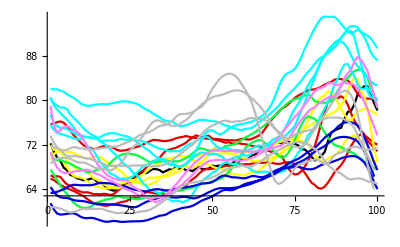

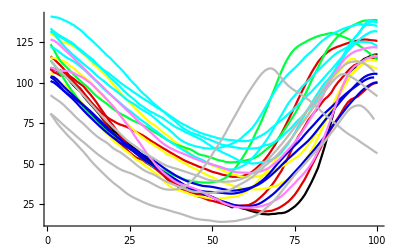

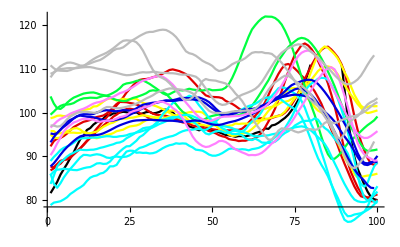

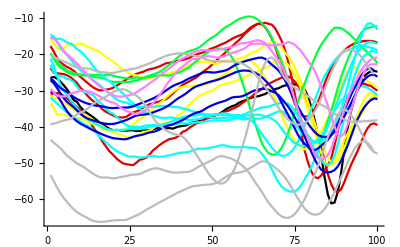

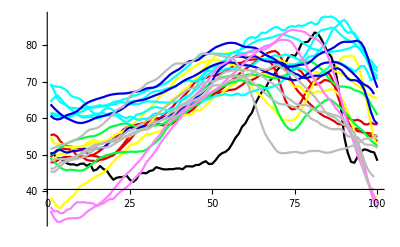

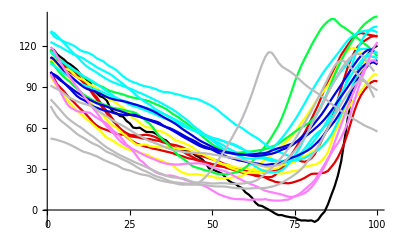

```mathematica
(*Plotsytle*)

ZERO=Setting[0.];
ONE=Setting[0.8823529411764706];
TWO=Setting[1.];
THREE=Setting[0.];
FOUR=Setting[0.];
FIVE=Setting[0.];
SIX=Setting[1.];
SEVEN = Setting[0.7372549019607844];

(*Femur*)
(*Vertical*)
RSAnimal0Trial1FEMVplot=ListLinePlot[RSAnimal0Trial1FEMV,PlotStyle->ZERO];
RSAnimal1Trial1FEMVplot=ListLinePlot[RSAnimal1Trial1FEMV,PlotStyle->ONE];
RSAnimal1Trial2FEMVplot=ListLinePlot[RSAnimal1Trial2FEMV,PlotStyle->ONE];
RSAnimal1Trial3FEMVplot=ListLinePlot[RSAnimal1Trial3FEMV,PlotStyle->ONE];
RSAnimal2Trial1FEMVplot=ListLinePlot[RSAnimal2Trial1FEMV,PlotStyle->TWO];
RSAnimal2Trial2FEMVplot=ListLinePlot[RSAnimal2Trial2FEMV,PlotStyle->TWO];
RSAnimal2Trial3FEMVplot=ListLinePlot[RSAnimal2Trial3FEMV,PlotStyle->TWO];
RSAnimal3Trial1FEMVplot=ListLinePlot[RSAnimal3Trial1FEMV,PlotStyle->THREE];
RSAnimal3Trial2FEMVplot=ListLinePlot[RSAnimal3Trial2FEMV,PlotStyle->THREE];
RSAnimal4Trial1FEMVplot=ListLinePlot[RSAnimal4Trial1FEMV,PlotStyle->FOUR];
RSAnimal4Trial2FEMVplot=ListLinePlot[RSAnimal4Trial2FEMV,PlotStyle->FOUR];
RSAnimal4Trial3FEMVplot=ListLinePlot[RSAnimal4Trial3FEMV,PlotStyle->FOUR];
RSAnimal4Trial4FEMVplot=ListLinePlot[RSAnimal4Trial4FEMV,PlotStyle->FOUR];
RSAnimal4Trial5FEMVplot=ListLinePlot[RSAnimal4Trial5FEMV,PlotStyle->FOUR];
RSAnimal5Trial1FEMVplot=ListLinePlot[RSAnimal5Trial1FEMV,PlotStyle->FIVE];
RSAnimal5Trial2FEMVplot=ListLinePlot[RSAnimal5Trial2FEMV,PlotStyle->FIVE];
RSAnimal5Trial3FEMVplot=ListLinePlot[RSAnimal5Trial3FEMV,PlotStyle->FIVE];
RSAnimal6Trial1FEMVplot=ListLinePlot[RSAnimal6Trial1FEMV,PlotStyle->SIX];
RSAnimal6Trial2FEMVplot=ListLinePlot[RSAnimal6Trial2FEMV,PlotStyle->SIX];
RSAnimal7Trial1FEMVplot=ListLinePlot[RSAnimal7Trial1FEMV,PlotStyle->SEVEN];
RSAnimal7Trial2FEMVplot=ListLinePlot[RSAnimal7Trial2FEMV,PlotStyle->SEVEN];
RSAnimal7Trial3FEMVplot=ListLinePlot[RSAnimal7Trial3FEMV,PlotStyle->SEVEN];
RSAnimal7Trial4FEMVplot=ListLinePlot[RSAnimal7Trial4FEMV,PlotStyle->SEVEN];

AllRSAnimal0FEMVplot=Show[RSAnimal0Trial1FEMVplot];
AllRSAnimal1FEMVplot=Show[RSAnimal1Trial1FEMVplot,RSAnimal1Trial2FEMVplot,RSAnimal1Trial3FEMVplot];
AllRSAnimal2FEMVplot=Show[RSAnimal2Trial1FEMVplot,RSAnimal2Trial2FEMVplot,RSAnimal2Trial3FEMVplot];
AllRSAnimal3FEMVplot=Show[RSAnimal3Trial1FEMVplot,RSAnimal3Trial2FEMVplot];
AllRSAnimal4FEMVplot=Show[RSAnimal4Trial1FEMVplot,RSAnimal4Trial2FEMVplot,RSAnimal4Trial3FEMVplot,RSAnimal4Trial4FEMVplot,RSAnimal4Trial5FEMVplot];
AllRSAnimal5FEMVplot=Show[RSAnimal5Trial1FEMVplot,RSAnimal5Trial2FEMVplot,RSAnimal5Trial3FEMVplot];
AllRSAnimal6FEMVplot=Show[RSAnimal6Trial1FEMVplot,RSAnimal6Trial2FEMVplot,PlotRange->All];
AllRSAnimal7FEMVplot=Show[RSAnimal7Trial1FEMVplot,RSAnimal7Trial2FEMVplot,RSAnimal7Trial3FEMVplot,RSAnimal7Trial4FEMVplot];
AllRSAnimalsAllTrialsFEMV=Show[AllRSAnimal0FEMVplot,AllRSAnimal1FEMVplot,AllRSAnimal2FEMVplot,AllRSAnimal3FEMVplot,AllRSAnimal4FEMVplot,AllRSAnimal5FEMVplot,AllRSAnimal6FEMVplot,AllRSAnimal7FEMVplot,PlotRange->All]

(*Horizontal*)
RSAnimal0Trial1FEMHplot=ListLinePlot[RSAnimal0Trial1FEMH,PlotStyle->ZERO];
RSAnimal1Trial1FEMHplot=ListLinePlot[RSAnimal1Trial1FEMH,PlotStyle->ONE];
RSAnimal1Trial2FEMHplot=ListLinePlot[RSAnimal1Trial2FEMH,PlotStyle->ONE];
RSAnimal1Trial3FEMHplot=ListLinePlot[RSAnimal1Trial3FEMH,PlotStyle->ONE];
RSAnimal2Trial1FEMHplot=ListLinePlot[RSAnimal2Trial1FEMH,PlotStyle->TWO];
RSAnimal2Trial2FEMHplot=ListLinePlot[RSAnimal2Trial2FEMH,PlotStyle->TWO];
RSAnimal2Trial3FEMHplot=ListLinePlot[RSAnimal2Trial3FEMH,PlotStyle->TWO];
RSAnimal3Trial1FEMHplot=ListLinePlot[RSAnimal3Trial1FEMH,PlotStyle->THREE];
RSAnimal3Trial2FEMHplot=ListLinePlot[RSAnimal3Trial2FEMH,PlotStyle->THREE];
RSAnimal4Trial1FEMHplot=ListLinePlot[RSAnimal4Trial1FEMH,PlotStyle->FOUR];
RSAnimal4Trial2FEMHplot=ListLinePlot[RSAnimal4Trial2FEMH,PlotStyle->FOUR];
RSAnimal4Trial3FEMHplot=ListLinePlot[RSAnimal4Trial3FEMH,PlotStyle->FOUR];
RSAnimal4Trial4FEMHplot=ListLinePlot[RSAnimal4Trial4FEMH,PlotStyle->FOUR];
RSAnimal4Trial5FEMHplot=ListLinePlot[RSAnimal4Trial5FEMH,PlotStyle->FOUR];
RSAnimal5Trial1FEMHplot=ListLinePlot[RSAnimal5Trial1FEMH,PlotStyle->FIVE];
RSAnimal5Trial2FEMHplot=ListLinePlot[RSAnimal5Trial2FEMH,PlotStyle->FIVE];
RSAnimal5Trial3FEMHplot=ListLinePlot[RSAnimal5Trial3FEMH,PlotStyle->FIVE];
RSAnimal6Trial1FEMHplot=ListLinePlot[RSAnimal6Trial1FEMH,PlotStyle->SIX];
RSAnimal6Trial2FEMHplot=ListLinePlot[RSAnimal6Trial2FEMH,PlotStyle->SIX];
RSAnimal7Trial1FEMHplot=ListLinePlot[RSAnimal7Trial1FEMH,PlotStyle->SEVEN];
RSAnimal7Trial2FEMHplot=ListLinePlot[RSAnimal7Trial2FEMH,PlotStyle->SEVEN];
RSAnimal7Trial3FEMHplot=ListLinePlot[RSAnimal7Trial3FEMH,PlotStyle->SEVEN];
RSAnimal7Trial4FEMHplot=ListLinePlot[RSAnimal7Trial4FEMH,PlotStyle->SEVEN];

AllRSAnimal0FEMHplot=Show[RSAnimal0Trial1FEMHplot];
AllRSAnimal1FEMHplot=Show[RSAnimal1Trial1FEMHplot,RSAnimal1Trial2FEMHplot,RSAnimal1Trial3FEMHplot];
AllRSAnimal2FEMHplot=Show[RSAnimal2Trial1FEMHplot,RSAnimal2Trial2FEMHplot,RSAnimal2Trial3FEMHplot];
AllRSAnimal3FEMHplot=Show[RSAnimal3Trial1FEMHplot,RSAnimal3Trial2FEMHplot];
AllRSAnimal4FEMHplot=Show[RSAnimal4Trial1FEMHplot,RSAnimal4Trial2FEMHplot,RSAnimal4Trial3FEMHplot,RSAnimal4Trial4FEMHplot,RSAnimal4Trial5FEMHplot];
AllRSAnimal5FEMHplot=Show[RSAnimal5Trial1FEMHplot,RSAnimal5Trial2FEMHplot,RSAnimal5Trial3FEMHplot];
AllRSAnimal6FEMHplot=Show[RSAnimal6Trial1FEMHplot,RSAnimal6Trial2FEMHplot,PlotRange->All];
AllRSAnimal7FEMHplot=Show[RSAnimal7Trial1FEMHplot,RSAnimal7Trial2FEMHplot,RSAnimal7Trial3FEMHplot,RSAnimal7Trial4FEMHplot];
AllRSAnimalsAllTrialsFEMH=Show[AllRSAnimal0FEMHplot,AllRSAnimal1FEMHplot,AllRSAnimal2FEMHplot,AllRSAnimal3FEMHplot,AllRSAnimal4FEMHplot,AllRSAnimal5FEMHplot,AllRSAnimal6FEMHplot,AllRSAnimal7FEMHplot,PlotRange->All]

(*TibFib*)
(*Vertical*)
RSAnimal0Trial1TIBVplot=ListLinePlot[RSAnimal0Trial1TIBV,PlotStyle->ZERO];
RSAnimal1Trial1TIBVplot=ListLinePlot[RSAnimal1Trial1TIBV,PlotStyle->ONE];
RSAnimal1Trial2TIBVplot=ListLinePlot[RSAnimal1Trial2TIBV,PlotStyle->ONE];
RSAnimal1Trial3TIBVplot=ListLinePlot[RSAnimal1Trial3TIBV,PlotStyle->ONE];
RSAnimal2Trial1TIBVplot=ListLinePlot[RSAnimal2Trial1TIBV,PlotStyle->TWO];
RSAnimal2Trial2TIBVplot=ListLinePlot[RSAnimal2Trial2TIBV,PlotStyle->TWO];
RSAnimal2Trial3TIBVplot=ListLinePlot[RSAnimal2Trial3TIBV,PlotStyle->TWO];
RSAnimal3Trial1TIBVplot=ListLinePlot[RSAnimal3Trial1TIBV,PlotStyle->THREE];
RSAnimal3Trial2TIBVplot=ListLinePlot[RSAnimal3Trial2TIBV,PlotStyle->THREE];
RSAnimal4Trial1TIBVplot=ListLinePlot[RSAnimal4Trial1TIBV,PlotStyle->FOUR];
RSAnimal4Trial2TIBVplot=ListLinePlot[RSAnimal4Trial2TIBV,PlotStyle->FOUR];
RSAnimal4Trial3TIBVplot=ListLinePlot[RSAnimal4Trial3TIBV,PlotStyle->FOUR];
RSAnimal4Trial4TIBVplot=ListLinePlot[RSAnimal4Trial4TIBV,PlotStyle->FOUR];
RSAnimal4Trial5TIBVplot=ListLinePlot[RSAnimal4Trial5TIBV,PlotStyle->FOUR];
RSAnimal5Trial1TIBVplot=ListLinePlot[RSAnimal5Trial1TIBV,PlotStyle->FIVE];
RSAnimal5Trial2TIBVplot=ListLinePlot[RSAnimal5Trial2TIBV,PlotStyle->FIVE];
RSAnimal5Trial3TIBVplot=ListLinePlot[RSAnimal5Trial3TIBV,PlotStyle->FIVE];
RSAnimal6Trial1TIBVplot=ListLinePlot[RSAnimal6Trial1TIBV,PlotStyle->SIX];
RSAnimal6Trial2TIBVplot=ListLinePlot[RSAnimal6Trial2TIBV,PlotStyle->SIX];
RSAnimal7Trial1TIBVplot=ListLinePlot[RSAnimal7Trial1TIBV,PlotStyle->SEVEN];
RSAnimal7Trial2TIBVplot=ListLinePlot[RSAnimal7Trial2TIBV,PlotStyle->SEVEN];
RSAnimal7Trial3TIBVplot=ListLinePlot[RSAnimal7Trial3TIBV,PlotStyle->SEVEN];
RSAnimal7Trial4TIBVplot=ListLinePlot[RSAnimal7Trial4TIBV,PlotStyle->SEVEN];

AllRSAnimal0TIBVplot=Show[RSAnimal0Trial1TIBVplot];
AllRSAnimal1TIBVplot=Show[RSAnimal1Trial1TIBVplot,RSAnimal1Trial2TIBVplot,RSAnimal1Trial3TIBVplot];
AllRSAnimal2TIBVplot=Show[RSAnimal2Trial1TIBVplot,RSAnimal2Trial2TIBVplot,RSAnimal2Trial3TIBVplot];
AllRSAnimal3TIBVplot=Show[RSAnimal3Trial1TIBVplot,RSAnimal3Trial2TIBVplot];
AllRSAnimal4TIBVplot=Show[RSAnimal4Trial1TIBVplot,RSAnimal4Trial2TIBVplot,RSAnimal4Trial3TIBVplot,RSAnimal4Trial4TIBVplot,RSAnimal4Trial5TIBVplot];
AllRSAnimal5TIBVplot=Show[RSAnimal5Trial1TIBVplot,RSAnimal5Trial2TIBVplot,RSAnimal5Trial3TIBVplot];
AllRSAnimal6TIBVplot=Show[RSAnimal6Trial1TIBVplot,RSAnimal6Trial2TIBVplot,PlotRange->All];
AllRSAnimal7TIBVplot=Show[RSAnimal7Trial1TIBVplot,RSAnimal7Trial2TIBVplot,RSAnimal7Trial3TIBVplot,RSAnimal7Trial4TIBVplot];
AllRSAnimalsAllTrialsTIBV=Show[AllRSAnimal0TIBVplot,AllRSAnimal1TIBVplot,AllRSAnimal2TIBVplot,AllRSAnimal3TIBVplot,AllRSAnimal4TIBVplot,AllRSAnimal5TIBVplot,AllRSAnimal6TIBVplot,AllRSAnimal7TIBVplot,PlotRange->All]

(*Horizontal*)
RSAnimal0Trial1TIBHplot=ListLinePlot[RSAnimal0Trial1TIBH,PlotStyle->ZERO];
RSAnimal1Trial1TIBHplot=ListLinePlot[RSAnimal1Trial1TIBH,PlotStyle->ONE];
RSAnimal1Trial2TIBHplot=ListLinePlot[RSAnimal1Trial2TIBH,PlotStyle->ONE];
RSAnimal1Trial3TIBHplot=ListLinePlot[RSAnimal1Trial3TIBH,PlotStyle->ONE];
RSAnimal2Trial1TIBHplot=ListLinePlot[RSAnimal2Trial1TIBH,PlotStyle->TWO];
RSAnimal2Trial2TIBHplot=ListLinePlot[RSAnimal2Trial2TIBH,PlotStyle->TWO];
RSAnimal2Trial3TIBHplot=ListLinePlot[RSAnimal2Trial3TIBH,PlotStyle->TWO];
RSAnimal3Trial1TIBHplot=ListLinePlot[RSAnimal3Trial1TIBH,PlotStyle->THREE];
RSAnimal3Trial2TIBHplot=ListLinePlot[RSAnimal3Trial2TIBH,PlotStyle->THREE];
RSAnimal4Trial1TIBHplot=ListLinePlot[RSAnimal4Trial1TIBH,PlotStyle->FOUR];
RSAnimal4Trial2TIBHplot=ListLinePlot[RSAnimal4Trial2TIBH,PlotStyle->FOUR];
RSAnimal4Trial3TIBHplot=ListLinePlot[RSAnimal4Trial3TIBH,PlotStyle->FOUR];
RSAnimal4Trial4TIBHplot=ListLinePlot[RSAnimal4Trial4TIBH,PlotStyle->FOUR];
RSAnimal4Trial5TIBHplot=ListLinePlot[RSAnimal4Trial5TIBH,PlotStyle->FOUR];
RSAnimal5Trial1TIBHplot=ListLinePlot[RSAnimal5Trial1TIBH,PlotStyle->FIVE];
RSAnimal5Trial2TIBHplot=ListLinePlot[RSAnimal5Trial2TIBH,PlotStyle->FIVE];
RSAnimal5Trial3TIBHplot=ListLinePlot[RSAnimal5Trial3TIBH,PlotStyle->FIVE];
RSAnimal6Trial1TIBHplot=ListLinePlot[RSAnimal6Trial1TIBH,PlotStyle->SIX];
RSAnimal6Trial2TIBHplot=ListLinePlot[RSAnimal6Trial2TIBH,PlotStyle->SIX];
RSAnimal7Trial1TIBHplot=ListLinePlot[RSAnimal7Trial1TIBH,PlotStyle->SEVEN];
RSAnimal7Trial2TIBHplot=ListLinePlot[RSAnimal7Trial2TIBH,PlotStyle->SEVEN];
RSAnimal7Trial3TIBHplot=ListLinePlot[RSAnimal7Trial3TIBH,PlotStyle->SEVEN];
RSAnimal7Trial4TIBHplot=ListLinePlot[RSAnimal7Trial4TIBH,PlotStyle->SEVEN];

AllRSAnimal0TIBHplot=Show[RSAnimal0Trial1TIBHplot];
AllRSAnimal1TIBHplot=Show[RSAnimal1Trial1TIBHplot,RSAnimal1Trial2TIBHplot,RSAnimal1Trial3TIBHplot];
AllRSAnimal2TIBHplot=Show[RSAnimal2Trial1TIBHplot,RSAnimal2Trial2TIBHplot,RSAnimal2Trial3TIBHplot];
AllRSAnimal3TIBHplot=Show[RSAnimal3Trial1TIBHplot,RSAnimal3Trial2TIBHplot];
AllRSAnimal4TIBHplot=Show[RSAnimal4Trial1TIBHplot,RSAnimal4Trial2TIBHplot,RSAnimal4Trial3TIBHplot,RSAnimal4Trial4TIBHplot,RSAnimal4Trial5TIBHplot];
AllRSAnimal5TIBHplot=Show[RSAnimal5Trial1TIBHplot,RSAnimal5Trial2TIBHplot,RSAnimal5Trial3TIBHplot];
AllRSAnimal6TIBHplot=Show[RSAnimal6Trial1TIBHplot,RSAnimal6Trial2TIBHplot,PlotRange->All];
AllRSAnimal7TIBHplot=Show[RSAnimal7Trial1TIBHplot,RSAnimal7Trial2TIBHplot,RSAnimal7Trial3TIBHplot,RSAnimal7Trial4TIBHplot];
AllRSAnimalsAllTrialsTIBH=Show[AllRSAnimal0TIBHplot,AllRSAnimal1TIBHplot,AllRSAnimal2TIBHplot,AllRSAnimal3TIBHplot,AllRSAnimal4TIBHplot,AllRSAnimal5TIBHplot,AllRSAnimal6TIBHplot,AllRSAnimal7TIBHplot,PlotRange->All]

(*Tarsals*)
(*Vertical*)
RSAnimal0Trial1TARVplot=ListLinePlot[RSAnimal0Trial1TARV,PlotStyle->ZERO];
RSAnimal1Trial1TARVplot=ListLinePlot[RSAnimal1Trial1TARV,PlotStyle->ONE];
RSAnimal1Trial2TARVplot=ListLinePlot[RSAnimal1Trial2TARV,PlotStyle->ONE];
RSAnimal1Trial3TARVplot=ListLinePlot[RSAnimal1Trial3TARV,PlotStyle->ONE];
RSAnimal2Trial1TARVplot=ListLinePlot[RSAnimal2Trial1TARV,PlotStyle->TWO];
RSAnimal2Trial2TARVplot=ListLinePlot[RSAnimal2Trial2TARV,PlotStyle->TWO];
RSAnimal2Trial3TARVplot=ListLinePlot[RSAnimal2Trial3TARV,PlotStyle->TWO];
RSAnimal3Trial1TARVplot=ListLinePlot[RSAnimal3Trial1TARV,PlotStyle->THREE];
RSAnimal3Trial2TARVplot=ListLinePlot[RSAnimal3Trial2TARV,PlotStyle->THREE];
RSAnimal4Trial1TARVplot=ListLinePlot[RSAnimal4Trial1TARV,PlotStyle->FOUR];
RSAnimal4Trial2TARVplot=ListLinePlot[RSAnimal4Trial2TARV,PlotStyle->FOUR];
RSAnimal4Trial3TARVplot=ListLinePlot[RSAnimal4Trial3TARV,PlotStyle->FOUR];
RSAnimal4Trial4TARVplot=ListLinePlot[RSAnimal4Trial4TARV,PlotStyle->FOUR];
RSAnimal4Trial5TARVplot=ListLinePlot[RSAnimal4Trial5TARV,PlotStyle->FOUR];
RSAnimal5Trial1TARVplot=ListLinePlot[RSAnimal5Trial1TARV,PlotStyle->FIVE];
RSAnimal5Trial2TARVplot=ListLinePlot[RSAnimal5Trial2TARV,PlotStyle->FIVE];
RSAnimal5Trial3TARVplot=ListLinePlot[RSAnimal5Trial3TARV,PlotStyle->FIVE];
RSAnimal6Trial1TARVplot=ListLinePlot[RSAnimal6Trial1TARV,PlotStyle->SIX];
RSAnimal6Trial2TARVplot=ListLinePlot[RSAnimal6Trial2TARV,PlotStyle->SIX];
RSAnimal7Trial1TARVplot=ListLinePlot[RSAnimal7Trial1TARV,PlotStyle->SEVEN];
RSAnimal7Trial2TARVplot=ListLinePlot[RSAnimal7Trial2TARV,PlotStyle->SEVEN];
RSAnimal7Trial3TARVplot=ListLinePlot[RSAnimal7Trial3TARV,PlotStyle->SEVEN];
RSAnimal7Trial4TARVplot=ListLinePlot[RSAnimal7Trial4TARV,PlotStyle->SEVEN];

AllRSAnimal0TARVplot=Show[RSAnimal0Trial1TARVplot];
AllRSAnimal1TARVplot=Show[RSAnimal1Trial1TARVplot,RSAnimal1Trial2TARVplot,RSAnimal1Trial3TARVplot];
AllRSAnimal2TARVplot=Show[RSAnimal2Trial1TARVplot,RSAnimal2Trial2TARVplot,RSAnimal2Trial3TARVplot];
AllRSAnimal3TARVplot=Show[RSAnimal3Trial1TARVplot,RSAnimal3Trial2TARVplot];
AllRSAnimal4TARVplot=Show[RSAnimal4Trial1TARVplot,RSAnimal4Trial2TARVplot,RSAnimal4Trial3TARVplot,RSAnimal4Trial4TARVplot,RSAnimal4Trial5TARVplot];
AllRSAnimal5TARVplot=Show[RSAnimal5Trial1TARVplot,RSAnimal5Trial2TARVplot,RSAnimal5Trial3TARVplot];
AllRSAnimal6TARVplot=Show[RSAnimal6Trial1TARVplot,RSAnimal6Trial2TARVplot,PlotRange->All];
AllRSAnimal7TARVplot=Show[RSAnimal7Trial1TARVplot,RSAnimal7Trial2TARVplot,RSAnimal7Trial3TARVplot,RSAnimal7Trial4TARVplot];
AllRSAnimalsAllTrialsTARV=Show[AllRSAnimal0TARVplot,AllRSAnimal1TARVplot,AllRSAnimal2TARVplot,AllRSAnimal3TARVplot,AllRSAnimal4TARVplot,AllRSAnimal5TARVplot,AllRSAnimal6TARVplot,AllRSAnimal7TARVplot,PlotRange->All]


(*Horizontal*)
RSAnimal0Trial1TARHplot=ListLinePlot[RSAnimal0Trial1TARH,PlotStyle->ZERO];
RSAnimal1Trial1TARHplot=ListLinePlot[RSAnimal1Trial1TARH,PlotStyle->ONE];
RSAnimal1Trial2TARHplot=ListLinePlot[RSAnimal1Trial2TARH,PlotStyle->ONE];
RSAnimal1Trial3TARHplot=ListLinePlot[RSAnimal1Trial3TARH,PlotStyle->ONE];
RSAnimal2Trial1TARHplot=ListLinePlot[RSAnimal2Trial1TARH,PlotStyle->TWO];
RSAnimal2Trial2TARHplot=ListLinePlot[RSAnimal2Trial2TARH,PlotStyle->TWO];
RSAnimal2Trial3TARHplot=ListLinePlot[RSAnimal2Trial3TARH,PlotStyle->TWO];
RSAnimal3Trial1TARHplot=ListLinePlot[RSAnimal3Trial1TARH,PlotStyle->THREE];
RSAnimal3Trial2TARHplot=ListLinePlot[RSAnimal3Trial2TARH,PlotStyle->THREE];
RSAnimal4Trial1TARHplot=ListLinePlot[RSAnimal4Trial1TARH,PlotStyle->FOUR];
RSAnimal4Trial2TARHplot=ListLinePlot[RSAnimal4Trial2TARH,PlotStyle->FOUR];
RSAnimal4Trial3TARHplot=ListLinePlot[RSAnimal4Trial3TARH,PlotStyle->FOUR];
RSAnimal4Trial4TARHplot=ListLinePlot[RSAnimal4Trial4TARH,PlotStyle->FOUR];
RSAnimal4Trial5TARHplot=ListLinePlot[RSAnimal4Trial5TARH,PlotStyle->FOUR];
RSAnimal5Trial1TARHplot=ListLinePlot[RSAnimal5Trial1TARH,PlotStyle->FIVE];
RSAnimal5Trial2TARHplot=ListLinePlot[RSAnimal5Trial2TARH,PlotStyle->FIVE];
RSAnimal5Trial3TARHplot=ListLinePlot[RSAnimal5Trial3TARH,PlotStyle->FIVE];
RSAnimal6Trial1TARHplot=ListLinePlot[RSAnimal6Trial1TARH,PlotStyle->SIX];
RSAnimal6Trial2TARHplot=ListLinePlot[RSAnimal6Trial2TARH,PlotStyle->SIX];
RSAnimal7Trial1TARHplot=ListLinePlot[RSAnimal7Trial1TARH,PlotStyle->SEVEN];
RSAnimal7Trial2TARHplot=ListLinePlot[RSAnimal7Trial2TARH,PlotStyle->SEVEN];
RSAnimal7Trial3TARHplot=ListLinePlot[RSAnimal7Trial3TARH,PlotStyle->SEVEN];
RSAnimal7Trial4TARHplot=ListLinePlot[RSAnimal7Trial4TARH,PlotStyle->SEVEN];

AllRSAnimal0TARHplot=Show[RSAnimal0Trial1TARHplot];
AllRSAnimal1TARHplot=Show[RSAnimal1Trial1TARHplot,RSAnimal1Trial2TARHplot,RSAnimal1Trial3TARHplot];
AllRSAnimal2TARHplot=Show[RSAnimal2Trial1TARHplot,RSAnimal2Trial2TARHplot,RSAnimal2Trial3TARHplot];
AllRSAnimal3TARHplot=Show[RSAnimal3Trial1TARHplot,RSAnimal3Trial2TARHplot];
AllRSAnimal4TARHplot=Show[RSAnimal4Trial1TARHplot,RSAnimal4Trial2TARHplot,RSAnimal4Trial3TARHplot,RSAnimal4Trial4TARHplot,RSAnimal4Trial5TARHplot];
AllRSAnimal5TARHplot=Show[RSAnimal5Trial1TARHplot,RSAnimal5Trial2TARHplot,RSAnimal5Trial3TARHplot];
AllRSAnimal6TARHplot=Show[RSAnimal6Trial1TARHplot,RSAnimal6Trial2TARHplot,PlotRange->All];
AllRSAnimal7TARHplot=Show[RSAnimal7Trial1TARHplot,RSAnimal7Trial2TARHplot,RSAnimal7Trial3TARHplot,RSAnimal7Trial4TARHplot];
AllRSAnimalsAllTrialsTARH=Show[AllRSAnimal0TARHplot,AllRSAnimal1TARHplot,AllRSAnimal2TARHplot,AllRSAnimal3TARHplot,AllRSAnimal4TARHplot,AllRSAnimal5TARHplot,AllRSAnimal6TARHplot,AllRSAnimal7TARHplot,PlotRange->All]
```

```mathematica
(* Pool the data for each joint*)

(*Femur*)
(*Vertical*)
AllRSTrialsFEMV=Table[Join[{RSAnimal0Trial1FEMV[[i]]},{RSAnimal1Trial1FEMV[[i]]},{RSAnimal1Trial2FEMV[[i]]},{RSAnimal1Trial3FEMV[[i]]},{RSAnimal2Trial1FEMV[[i]]},{RSAnimal2Trial2FEMV[[i]]},{RSAnimal2Trial3FEMV[[i]]},{RSAnimal3Trial1FEMV[[i]]},{RSAnimal3Trial2FEMV[[i]]},{RSAnimal4Trial1FEMV[[i]]},{RSAnimal4Trial2FEMV[[i]]},{RSAnimal4Trial3FEMV[[i]]},{RSAnimal4Trial4FEMV[[i]]},{RSAnimal4Trial5FEMV[[i]]},{RSAnimal5Trial1FEMV[[i]]},{RSAnimal5Trial2FEMV[[i]]},{RSAnimal5Trial3FEMV[[i]]},{RSAnimal6Trial1FEMV[[i]]},{RSAnimal6Trial2FEMV[[i]]},{RSAnimal7Trial1FEMV[[i]]},{RSAnimal7Trial2FEMV[[i]]},{RSAnimal7Trial3FEMV[[i]]},{RSAnimal7Trial4FEMV[[i]]}],{i,1,99}];
Dimensions[AllRSTrialsFEMV];(*{100,8} - 100 rows for each data point, 8 columns for 8 trials*)

(*Horizontal*)
AllRSTrialsFEMH=Table[Join[{RSAnimal0Trial1FEMH[[i]]},{RSAnimal1Trial1FEMH[[i]]},{RSAnimal1Trial2FEMH[[i]]},{RSAnimal1Trial3FEMH[[i]]},{RSAnimal2Trial1FEMH[[i]]},{RSAnimal2Trial2FEMH[[i]]},{RSAnimal2Trial3FEMH[[i]]},{RSAnimal3Trial1FEMH[[i]]},{RSAnimal3Trial2FEMH[[i]]},{RSAnimal4Trial1FEMH[[i]]},{RSAnimal4Trial2FEMH[[i]]},{RSAnimal4Trial3FEMH[[i]]},{RSAnimal4Trial4FEMH[[i]]},{RSAnimal4Trial5FEMH[[i]]},{RSAnimal5Trial1FEMH[[i]]},{RSAnimal5Trial2FEMH[[i]]},{RSAnimal5Trial3FEMH[[i]]},{RSAnimal6Trial1FEMH[[i]]},{RSAnimal6Trial2FEMH[[i]]},{RSAnimal7Trial1FEMH[[i]]},{RSAnimal7Trial2FEMH[[i]]},{RSAnimal7Trial3FEMH[[i]]},{RSAnimal7Trial4FEMH[[i]]}],{i,1,99}];
Dimensions[AllRSTrialsFEMH];(*{100,8} - 100 rows for each data point, 8 columns for 8 trials*)

(*TibFib*)
(*Vertical*)
AllRSTrialsTIBV=Table[Join[{RSAnimal0Trial1TIBV[[i]]},{RSAnimal1Trial1TIBV[[i]]},{RSAnimal1Trial2TIBV[[i]]},{RSAnimal1Trial3TIBV[[i]]},{RSAnimal2Trial1TIBV[[i]]},{RSAnimal2Trial2TIBV[[i]]},{RSAnimal2Trial3TIBV[[i]]},{RSAnimal3Trial1TIBV[[i]]},{RSAnimal3Trial2TIBV[[i]]},{RSAnimal4Trial1TIBV[[i]]},{RSAnimal4Trial2TIBV[[i]]},{RSAnimal4Trial3TIBV[[i]]},{RSAnimal4Trial4TIBV[[i]]},{RSAnimal4Trial5TIBV[[i]]},{RSAnimal5Trial1TIBV[[i]]},{RSAnimal5Trial2TIBV[[i]]},{RSAnimal5Trial3TIBV[[i]]},{RSAnimal6Trial1TIBV[[i]]},{RSAnimal6Trial2TIBV[[i]]},{RSAnimal7Trial1TIBV[[i]]},{RSAnimal7Trial2TIBV[[i]]},{RSAnimal7Trial3TIBV[[i]]},{RSAnimal7Trial4TIBV[[i]]}],{i,1,99}];
Dimensions[AllRSTrialsTIBV];(*{100,8} - 100 rows for each data point, 8 columns for 8 trials*)

(*Horizontal*)
AllRSTrialsTIBH=Table[Join[{RSAnimal0Trial1TIBH[[i]]},{RSAnimal1Trial1TIBH[[i]]},{RSAnimal1Trial2TIBH[[i]]},{RSAnimal1Trial3TIBH[[i]]},{RSAnimal2Trial1TIBH[[i]]},{RSAnimal2Trial2TIBH[[i]]},{RSAnimal2Trial3TIBH[[i]]},{RSAnimal3Trial1TIBH[[i]]},{RSAnimal3Trial2TIBH[[i]]},{RSAnimal4Trial1TIBH[[i]]},{RSAnimal4Trial2TIBH[[i]]},{RSAnimal4Trial3TIBH[[i]]},{RSAnimal4Trial4TIBH[[i]]},{RSAnimal4Trial5TIBH[[i]]},{RSAnimal5Trial1TIBH[[i]]},{RSAnimal5Trial2TIBH[[i]]},{RSAnimal5Trial3TIBH[[i]]},{RSAnimal6Trial1TIBH[[i]]},{RSAnimal6Trial2TIBH[[i]]},{RSAnimal7Trial1TIBH[[i]]},{RSAnimal7Trial2TIBH[[i]]},{RSAnimal7Trial3TIBH[[i]]},{RSAnimal7Trial4TIBH[[i]]}],{i,1,99}];
Dimensions[AllRSTrialsTIBH];(*{100,8} - 100 rows for each data point, 8 columns for 8 trials*)

(*Tarsals*)
(*Vertical*)
AllRSTrialsTARV=Table[Join[{RSAnimal0Trial1TARV[[i]]},{RSAnimal1Trial1TARV[[i]]},{RSAnimal1Trial2TARV[[i]]},{RSAnimal1Trial3TARV[[i]]},{RSAnimal2Trial1TARV[[i]]},{RSAnimal2Trial2TARV[[i]]},{RSAnimal2Trial3TARV[[i]]},{RSAnimal3Trial1TARV[[i]]},{RSAnimal3Trial2TARV[[i]]},{RSAnimal4Trial1TARV[[i]]},{RSAnimal4Trial2TARV[[i]]},{RSAnimal4Trial3TARV[[i]]},{RSAnimal4Trial4TARV[[i]]},{RSAnimal4Trial5TARV[[i]]},{RSAnimal5Trial1TARV[[i]]},{RSAnimal5Trial2TARV[[i]]},{RSAnimal5Trial3TARV[[i]]},{RSAnimal6Trial1TARV[[i]]},{RSAnimal6Trial2TARV[[i]]},{RSAnimal7Trial1TARV[[i]]},{RSAnimal7Trial2TARV[[i]]},{RSAnimal7Trial3TARV[[i]]},{RSAnimal7Trial4TARV[[i]]}],{i,1,99}];
Dimensions[AllRSTrialsTARV];(*{100,8} - 100 rows for each data point, 8 columns for 8 trials*)

(*Horizontal*)
AllRSTrialsTARH=Table[Join[{RSAnimal0Trial1TARH[[i]]},{RSAnimal1Trial1TARH[[i]]},{RSAnimal1Trial2TARH[[i]]},{RSAnimal1Trial3TARH[[i]]},{RSAnimal2Trial1TARH[[i]]},{RSAnimal2Trial2TARH[[i]]},{RSAnimal2Trial3TARH[[i]]},{RSAnimal3Trial1TARH[[i]]},{RSAnimal3Trial2TARH[[i]]},{RSAnimal4Trial1TARH[[i]]},{RSAnimal4Trial2TARH[[i]]},{RSAnimal4Trial3TARH[[i]]},{RSAnimal4Trial4TARH[[i]]},{RSAnimal4Trial5TARH[[i]]},{RSAnimal5Trial1TARH[[i]]},{RSAnimal5Trial2TARH[[i]]},{RSAnimal5Trial3TARH[[i]]},{RSAnimal6Trial1TARH[[i]]},{RSAnimal6Trial2TARH[[i]]},{RSAnimal7Trial1TARH[[i]]},{RSAnimal7Trial2TARH[[i]]},{RSAnimal7Trial3TARH[[i]]},{RSAnimal7Trial4TARH[[i]]}],{i,1,99}];
Dimensions[AllRSTrialsTARH]; (*{100,8} - 100 rows for each data point 8 columns for 8 trials*)
```

```mathematica
(*Calculate mean and SD - then add and substract SD from mean*)

(*Femur*)
(*Vertical*)
MeanFEMVData=Table[Mean[AllRSTrialsFEMV[[i,All]]],{i,1,99}];
SDFEMVData=Table[StandardDeviation[AllRSTrialsFEMV[[i,All]]],{i,1,99}];

MeanPlusSDFEMVData=Table[MeanFEMVData[[i]]+SDFEMVData[[i]],{i,1,99}];
MeanMinusSDFEMVData=Table[MeanFEMVData[[i]]-SDFEMVData[[i]],{i,1,99}];

(*Horizontal*)
MeanFEMHData=Table[Mean[AllRSTrialsFEMH[[i,All]]],{i,1,99}];
SDFEMHData=Table[StandardDeviation[AllRSTrialsFEMH[[i,All]]],{i,1,99}];

MeanPlusSDFEMHData=Table[MeanFEMHData[[i]]+SDFEMHData[[i]],{i,1,99}];
MeanMinusSDFEMHData=Table[MeanFEMHData[[i]]-SDFEMHData[[i]],{i,1,99}];


(*TibFib*)
(*Vertical*)
MeanTIBVData=Table[Mean[AllRSTrialsTIBV[[i,All]]],{i,1,99}];
SDTIBVData=Table[StandardDeviation[AllRSTrialsTIBV[[i,All]]],{i,1,99}];

MeanPlusSDTIBVData=Table[MeanTIBVData[[i]]+SDTIBVData[[i]],{i,1,99}];
MeanMinusSDTIBVData=Table[MeanTIBVData[[i]]-SDTIBVData[[i]],{i,1,99}];

(*Horizontal*)
MeanTIBHData=Table[Mean[AllRSTrialsTIBH[[i,All]]],{i,1,99}];
SDTIBHData=Table[StandardDeviation[AllRSTrialsTIBH[[i,All]]],{i,1,99}];

MeanPlusSDTIBHData=Table[MeanTIBHData[[i]]+SDTIBHData[[i]],{i,1,99}];
MeanMinusSDTIBHData=Table[MeanTIBHData[[i]]-SDTIBHData[[i]],{i,1,99}];


(*Tarsals*)
(*Vertical*)
MeanTARVData=Table[Mean[AllRSTrialsTARV[[i,All]]],{i,1,99}];
SDTARVData=Table[StandardDeviation[AllRSTrialsTARV[[i,All]]],{i,1,99}];

MeanPlusSDTARVData=Table[MeanTARVData[[i]]+SDTARVData[[i]],{i,1,99}];
MeanMinusSDTARVData=Table[MeanTARVData[[i]]-SDTARVData[[i]],{i,1,99}];

(*Horizontal*)
MeanTARHData=Table[Mean[AllRSTrialsTARH[[i,All]]],{i,1,99}];
SDTARHData=Table[StandardDeviation[AllRSTrialsTARH[[i,All]]],{i,1,99}];

MeanPlusSDTARHData=Table[MeanTARHData[[i]]+SDTARHData[[i]],{i,1,99}];
MeanMinusSDTARHData=Table[MeanTARHData[[i]]-SDTARHData[[i]],{i,1,99}];
```

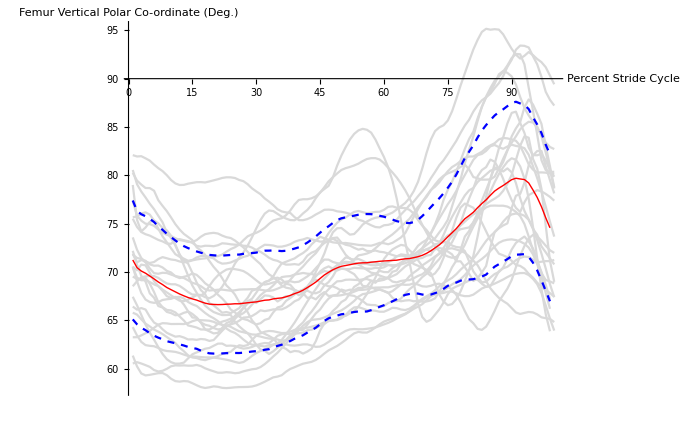

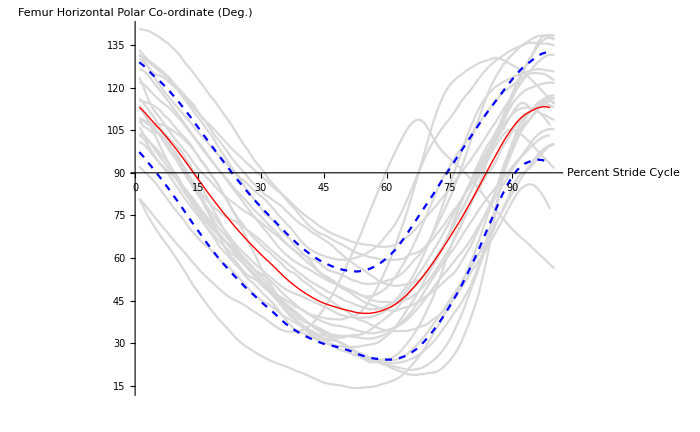

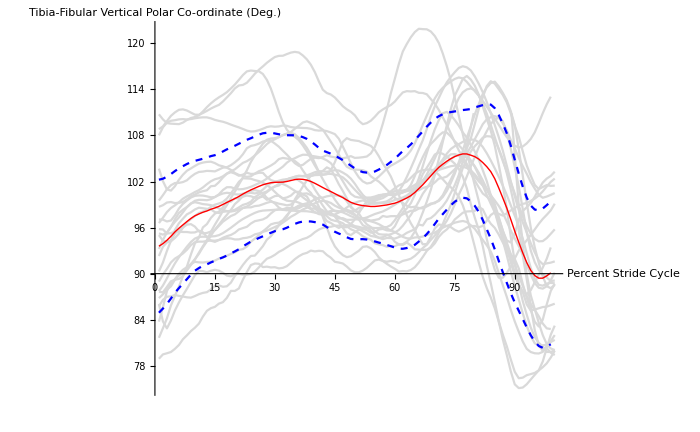

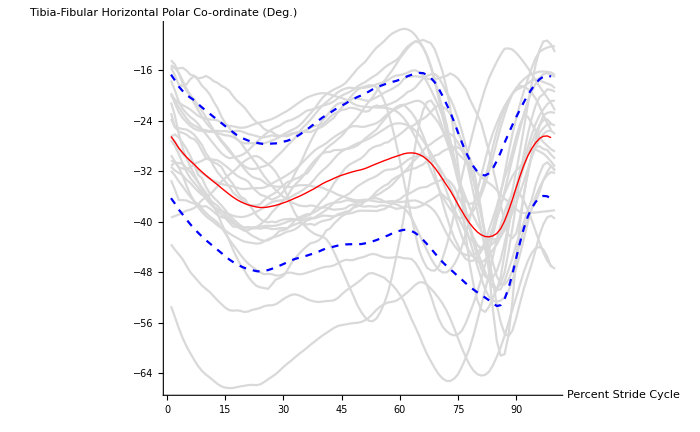

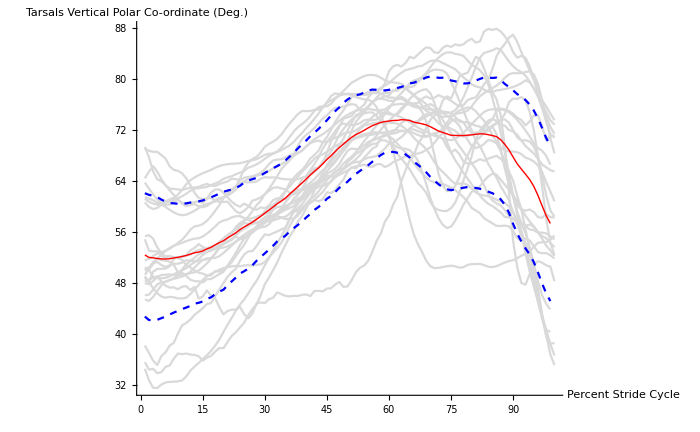

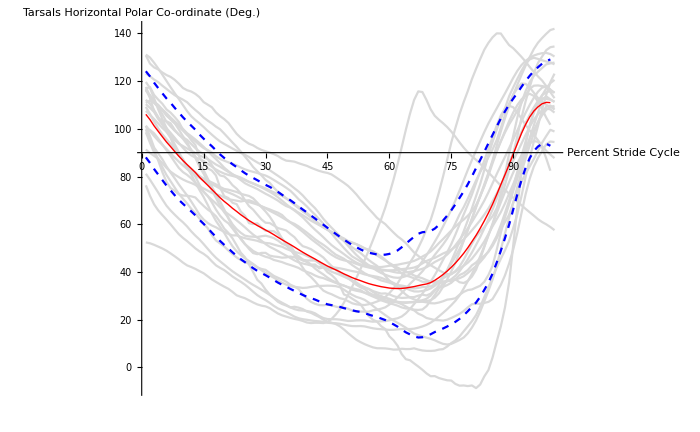

```mathematica
(*Create Mean +/-SD joint angle plots*)

(*Plot styles and settings*)
Meanplot={Thick,Red};
SDplot={Dashed,Blue};
AllTrialsplot={LightGray};
MeanSDplotrangeh={150,-70};
MeanSDplotrangev={150,-70};

(*Femur*)
(*Vertical*)
RSAnimal0Trial1FEMVplot=ListLinePlot[RSAnimal0Trial1FEMV,PlotStyle->AllTrialsplot];
RSAnimal1Trial1FEMVplot=ListLinePlot[RSAnimal1Trial1FEMV,PlotStyle->AllTrialsplot];
RSAnimal1Trial2FEMVplot=ListLinePlot[RSAnimal1Trial2FEMV,PlotStyle->AllTrialsplot];
RSAnimal1Trial3FEMVplot=ListLinePlot[RSAnimal1Trial3FEMV,PlotStyle->AllTrialsplot];
RSAnimal2Trial1FEMVplot=ListLinePlot[RSAnimal2Trial1FEMV,PlotStyle->AllTrialsplot];
RSAnimal2Trial2FEMVplot=ListLinePlot[RSAnimal2Trial2FEMV,PlotStyle->AllTrialsplot];
RSAnimal2Trial3FEMVplot=ListLinePlot[RSAnimal2Trial3FEMV,PlotStyle->AllTrialsplot];
RSAnimal3Trial1FEMVplot=ListLinePlot[RSAnimal3Trial1FEMV,PlotStyle->AllTrialsplot];
RSAnimal3Trial2FEMVplot=ListLinePlot[RSAnimal3Trial2FEMV,PlotStyle->AllTrialsplot];
RSAnimal4Trial1FEMVplot=ListLinePlot[RSAnimal4Trial1FEMV,PlotStyle->AllTrialsplot];
RSAnimal4Trial2FEMVplot=ListLinePlot[RSAnimal4Trial2FEMV,PlotStyle->AllTrialsplot];
RSAnimal4Trial3FEMVplot=ListLinePlot[RSAnimal4Trial3FEMV,PlotStyle->AllTrialsplot];
RSAnimal4Trial4FEMVplot=ListLinePlot[RSAnimal4Trial4FEMV,PlotStyle->AllTrialsplot];
RSAnimal4Trial5FEMVplot=ListLinePlot[RSAnimal4Trial5FEMV,PlotStyle->AllTrialsplot];
RSAnimal5Trial1FEMVplot=ListLinePlot[RSAnimal5Trial1FEMV,PlotStyle->AllTrialsplot];
RSAnimal5Trial2FEMVplot=ListLinePlot[RSAnimal5Trial2FEMV,PlotStyle->AllTrialsplot];
RSAnimal5Trial3FEMVplot=ListLinePlot[RSAnimal5Trial3FEMV,PlotStyle->AllTrialsplot];
RSAnimal6Trial1FEMVplot=ListLinePlot[RSAnimal6Trial1FEMV,PlotStyle->AllTrialsplot];
RSAnimal6Trial2FEMVplot=ListLinePlot[RSAnimal6Trial2FEMV,PlotStyle->AllTrialsplot];
RSAnimal7Trial1FEMVplot=ListLinePlot[RSAnimal7Trial1FEMV,PlotStyle->AllTrialsplot];
RSAnimal7Trial2FEMVplot=ListLinePlot[RSAnimal7Trial2FEMV,PlotStyle->AllTrialsplot];
RSAnimal7Trial3FEMVplot=ListLinePlot[RSAnimal7Trial3FEMV,PlotStyle->AllTrialsplot];
RSAnimal7Trial4FEMVplot=ListLinePlot[RSAnimal7Trial4FEMV,PlotStyle->AllTrialsplot];

AllRSAnimal0FEMVplot=Show[RSAnimal0Trial1FEMVplot];
AllRSAnimal1FEMVplot=Show[RSAnimal1Trial1FEMVplot,RSAnimal1Trial2FEMVplot,RSAnimal1Trial3FEMVplot];
AllRSAnimal2FEMVplot=Show[RSAnimal2Trial1FEMVplot,RSAnimal2Trial2FEMVplot,RSAnimal2Trial3FEMVplot];
AllRSAnimal3FEMVplot=Show[RSAnimal3Trial1FEMVplot,RSAnimal3Trial2FEMVplot];
AllRSAnimal4FEMVplot=Show[RSAnimal4Trial1FEMVplot,RSAnimal4Trial2FEMVplot,RSAnimal4Trial3FEMVplot,RSAnimal4Trial4FEMVplot,RSAnimal4Trial5FEMVplot];
AllRSAnimal5FEMVplot=Show[RSAnimal5Trial1FEMVplot,RSAnimal5Trial2FEMVplot,RSAnimal5Trial3FEMVplot];
AllRSAnimal6FEMVplot=Show[RSAnimal6Trial1FEMVplot,RSAnimal6Trial2FEMVplot,PlotRange->All];
AllRSAnimal7FEMVplot=Show[RSAnimal7Trial1FEMVplot,RSAnimal7Trial2FEMVplot,RSAnimal7Trial3FEMVplot,RSAnimal7Trial4FEMVplot];
AllRSAnimalsAllTrialsFEMV=Show[AllRSAnimal0FEMVplot,AllRSAnimal1FEMVplot,AllRSAnimal2FEMVplot,AllRSAnimal3FEMVplot,AllRSAnimal4FEMVplot,AllRSAnimal5FEMVplot,AllRSAnimal6FEMVplot,AllRSAnimal7FEMVplot,PlotRange->All];

(*Horizontal*)
RSAnimal0Trial1FEMHplot=ListLinePlot[RSAnimal0Trial1FEMH,PlotStyle->AllTrialsplot];
RSAnimal1Trial1FEMHplot=ListLinePlot[RSAnimal1Trial1FEMH,PlotStyle->AllTrialsplot];
RSAnimal1Trial2FEMHplot=ListLinePlot[RSAnimal1Trial2FEMH,PlotStyle->AllTrialsplot];
RSAnimal1Trial3FEMHplot=ListLinePlot[RSAnimal1Trial3FEMH,PlotStyle->AllTrialsplot];
RSAnimal2Trial1FEMHplot=ListLinePlot[RSAnimal2Trial1FEMH,PlotStyle->AllTrialsplot];
RSAnimal2Trial2FEMHplot=ListLinePlot[RSAnimal2Trial2FEMH,PlotStyle->AllTrialsplot];
RSAnimal2Trial3FEMHplot=ListLinePlot[RSAnimal2Trial3FEMH,PlotStyle->AllTrialsplot];
RSAnimal3Trial1FEMHplot=ListLinePlot[RSAnimal3Trial1FEMH,PlotStyle->AllTrialsplot];
RSAnimal3Trial2FEMHplot=ListLinePlot[RSAnimal3Trial2FEMH,PlotStyle->AllTrialsplot];
RSAnimal4Trial1FEMHplot=ListLinePlot[RSAnimal4Trial1FEMH,PlotStyle->AllTrialsplot];
RSAnimal4Trial2FEMHplot=ListLinePlot[RSAnimal4Trial2FEMH,PlotStyle->AllTrialsplot];
RSAnimal4Trial3FEMHplot=ListLinePlot[RSAnimal4Trial3FEMH,PlotStyle->AllTrialsplot];
RSAnimal4Trial4FEMHplot=ListLinePlot[RSAnimal4Trial4FEMH,PlotStyle->AllTrialsplot];
RSAnimal4Trial5FEMHplot=ListLinePlot[RSAnimal4Trial5FEMH,PlotStyle->AllTrialsplot];
RSAnimal5Trial1FEMHplot=ListLinePlot[RSAnimal5Trial1FEMH,PlotStyle->AllTrialsplot];
RSAnimal5Trial2FEMHplot=ListLinePlot[RSAnimal5Trial2FEMH,PlotStyle->AllTrialsplot];
RSAnimal5Trial3FEMHplot=ListLinePlot[RSAnimal5Trial3FEMH,PlotStyle->AllTrialsplot];
RSAnimal6Trial1FEMHplot=ListLinePlot[RSAnimal6Trial1FEMH,PlotStyle->AllTrialsplot];
RSAnimal6Trial2FEMHplot=ListLinePlot[RSAnimal6Trial2FEMH,PlotStyle->AllTrialsplot];
RSAnimal7Trial1FEMHplot=ListLinePlot[RSAnimal7Trial1FEMH,PlotStyle->AllTrialsplot];
RSAnimal7Trial2FEMHplot=ListLinePlot[RSAnimal7Trial2FEMH,PlotStyle->AllTrialsplot];
RSAnimal7Trial3FEMHplot=ListLinePlot[RSAnimal7Trial3FEMH,PlotStyle->AllTrialsplot];
RSAnimal7Trial4FEMHplot=ListLinePlot[RSAnimal7Trial4FEMH,PlotStyle->AllTrialsplot];

AllRSAnimal0FEMHplot=Show[RSAnimal0Trial1FEMHplot];
AllRSAnimal1FEMHplot=Show[RSAnimal1Trial1FEMHplot,RSAnimal1Trial2FEMHplot,RSAnimal1Trial3FEMHplot];
AllRSAnimal2FEMHplot=Show[RSAnimal2Trial1FEMHplot,RSAnimal2Trial2FEMHplot,RSAnimal2Trial3FEMHplot];
AllRSAnimal3FEMHplot=Show[RSAnimal3Trial1FEMHplot,RSAnimal3Trial2FEMHplot];
AllRSAnimal4FEMHplot=Show[RSAnimal4Trial1FEMHplot,RSAnimal4Trial2FEMHplot,RSAnimal4Trial3FEMHplot,RSAnimal4Trial4FEMHplot,RSAnimal4Trial5FEMHplot];
AllRSAnimal5FEMHplot=Show[RSAnimal5Trial1FEMHplot,RSAnimal5Trial2FEMHplot,RSAnimal5Trial3FEMHplot];
AllRSAnimal6FEMHplot=Show[RSAnimal6Trial1FEMHplot,RSAnimal6Trial2FEMHplot,PlotRange->All];
AllRSAnimal7FEMHplot=Show[RSAnimal7Trial1FEMHplot,RSAnimal7Trial2FEMHplot,RSAnimal7Trial3FEMHplot,RSAnimal7Trial4FEMHplot];
AllRSAnimalsAllTrialsFEMH=Show[AllRSAnimal0FEMHplot,AllRSAnimal1FEMHplot,AllRSAnimal2FEMHplot,AllRSAnimal3FEMHplot,AllRSAnimal4FEMHplot,AllRSAnimal5FEMHplot,AllRSAnimal6FEMHplot,AllRSAnimal7FEMHplot,PlotRange->All];

(*TibFib*)
(*Vertical*)
RSAnimal0Trial1TIBVplot=ListLinePlot[RSAnimal0Trial1TIBV,PlotStyle->AllTrialsplot];
RSAnimal1Trial1TIBVplot=ListLinePlot[RSAnimal1Trial1TIBV,PlotStyle->AllTrialsplot];
RSAnimal1Trial2TIBVplot=ListLinePlot[RSAnimal1Trial2TIBV,PlotStyle->AllTrialsplot];
RSAnimal1Trial3TIBVplot=ListLinePlot[RSAnimal1Trial3TIBV,PlotStyle->AllTrialsplot];
RSAnimal2Trial1TIBVplot=ListLinePlot[RSAnimal2Trial1TIBV,PlotStyle->AllTrialsplot];
RSAnimal2Trial2TIBVplot=ListLinePlot[RSAnimal2Trial2TIBV,PlotStyle->AllTrialsplot];
RSAnimal2Trial3TIBVplot=ListLinePlot[RSAnimal2Trial3TIBV,PlotStyle->AllTrialsplot];
RSAnimal3Trial1TIBVplot=ListLinePlot[RSAnimal3Trial1TIBV,PlotStyle->AllTrialsplot];
RSAnimal3Trial2TIBVplot=ListLinePlot[RSAnimal3Trial2TIBV,PlotStyle->AllTrialsplot];
RSAnimal4Trial1TIBVplot=ListLinePlot[RSAnimal4Trial1TIBV,PlotStyle->AllTrialsplot];
RSAnimal4Trial2TIBVplot=ListLinePlot[RSAnimal4Trial2TIBV,PlotStyle->AllTrialsplot];
RSAnimal4Trial3TIBVplot=ListLinePlot[RSAnimal4Trial3TIBV,PlotStyle->AllTrialsplot];
RSAnimal4Trial4TIBVplot=ListLinePlot[RSAnimal4Trial4TIBV,PlotStyle->AllTrialsplot];
RSAnimal4Trial5TIBVplot=ListLinePlot[RSAnimal4Trial5TIBV,PlotStyle->AllTrialsplot];
RSAnimal5Trial1TIBVplot=ListLinePlot[RSAnimal5Trial1TIBV,PlotStyle->AllTrialsplot];
RSAnimal5Trial2TIBVplot=ListLinePlot[RSAnimal5Trial2TIBV,PlotStyle->AllTrialsplot];
RSAnimal5Trial3TIBVplot=ListLinePlot[RSAnimal5Trial3TIBV,PlotStyle->AllTrialsplot];
RSAnimal6Trial1TIBVplot=ListLinePlot[RSAnimal6Trial1TIBV,PlotStyle->AllTrialsplot];
RSAnimal6Trial2TIBVplot=ListLinePlot[RSAnimal6Trial2TIBV,PlotStyle->AllTrialsplot];
RSAnimal7Trial1TIBVplot=ListLinePlot[RSAnimal7Trial1TIBV,PlotStyle->AllTrialsplot];
RSAnimal7Trial2TIBVplot=ListLinePlot[RSAnimal7Trial2TIBV,PlotStyle->AllTrialsplot];
RSAnimal7Trial3TIBVplot=ListLinePlot[RSAnimal7Trial3TIBV,PlotStyle->AllTrialsplot];
RSAnimal7Trial4TIBVplot=ListLinePlot[RSAnimal7Trial4TIBV,PlotStyle->AllTrialsplot];

AllRSAnimal0TIBVplot=Show[RSAnimal0Trial1TIBVplot];
AllRSAnimal1TIBVplot=Show[RSAnimal1Trial1TIBVplot,RSAnimal1Trial2TIBVplot,RSAnimal1Trial3TIBVplot];
AllRSAnimal2TIBVplot=Show[RSAnimal2Trial1TIBVplot,RSAnimal2Trial2TIBVplot,RSAnimal2Trial3TIBVplot];
AllRSAnimal3TIBVplot=Show[RSAnimal3Trial1TIBVplot,RSAnimal3Trial2TIBVplot];
AllRSAnimal4TIBVplot=Show[RSAnimal4Trial1TIBVplot,RSAnimal4Trial2TIBVplot,RSAnimal4Trial3TIBVplot,RSAnimal4Trial4TIBVplot,RSAnimal4Trial5TIBVplot];
AllRSAnimal5TIBVplot=Show[RSAnimal5Trial1TIBVplot,RSAnimal5Trial2TIBVplot,RSAnimal5Trial3TIBVplot];
AllRSAnimal6TIBVplot=Show[RSAnimal6Trial1TIBVplot,RSAnimal6Trial2TIBVplot,PlotRange->All];
AllRSAnimal7TIBVplot=Show[RSAnimal7Trial1TIBVplot,RSAnimal7Trial2TIBVplot,RSAnimal7Trial3TIBVplot,RSAnimal7Trial4TIBVplot];
AllRSAnimalsAllTrialsTIBV=Show[AllRSAnimal0TIBVplot,AllRSAnimal1TIBVplot,AllRSAnimal2TIBVplot,AllRSAnimal3TIBVplot,AllRSAnimal4TIBVplot,AllRSAnimal5TIBVplot,AllRSAnimal6TIBVplot,AllRSAnimal7TIBVplot,PlotRange->All];

(*Horizontal*)
RSAnimal0Trial1TIBHplot=ListLinePlot[RSAnimal0Trial1TIBH,PlotStyle->AllTrialsplot];
RSAnimal1Trial1TIBHplot=ListLinePlot[RSAnimal1Trial1TIBH,PlotStyle->AllTrialsplot];
RSAnimal1Trial2TIBHplot=ListLinePlot[RSAnimal1Trial2TIBH,PlotStyle->AllTrialsplot];
RSAnimal1Trial3TIBHplot=ListLinePlot[RSAnimal1Trial3TIBH,PlotStyle->AllTrialsplot];
RSAnimal2Trial1TIBHplot=ListLinePlot[RSAnimal2Trial1TIBH,PlotStyle->AllTrialsplot];
RSAnimal2Trial2TIBHplot=ListLinePlot[RSAnimal2Trial2TIBH,PlotStyle->AllTrialsplot];
RSAnimal2Trial3TIBHplot=ListLinePlot[RSAnimal2Trial3TIBH,PlotStyle->AllTrialsplot];
RSAnimal3Trial1TIBHplot=ListLinePlot[RSAnimal3Trial1TIBH,PlotStyle->AllTrialsplot];
RSAnimal3Trial2TIBHplot=ListLinePlot[RSAnimal3Trial2TIBH,PlotStyle->AllTrialsplot];
RSAnimal4Trial1TIBHplot=ListLinePlot[RSAnimal4Trial1TIBH,PlotStyle->AllTrialsplot];
RSAnimal4Trial2TIBHplot=ListLinePlot[RSAnimal4Trial2TIBH,PlotStyle->AllTrialsplot];
RSAnimal4Trial3TIBHplot=ListLinePlot[RSAnimal4Trial3TIBH,PlotStyle->AllTrialsplot];
RSAnimal4Trial4TIBHplot=ListLinePlot[RSAnimal4Trial4TIBH,PlotStyle->AllTrialsplot];
RSAnimal4Trial5TIBHplot=ListLinePlot[RSAnimal4Trial5TIBH,PlotStyle->AllTrialsplot];
RSAnimal5Trial1TIBHplot=ListLinePlot[RSAnimal5Trial1TIBH,PlotStyle->AllTrialsplot];
RSAnimal5Trial2TIBHplot=ListLinePlot[RSAnimal5Trial2TIBH,PlotStyle->AllTrialsplot];
RSAnimal5Trial3TIBHplot=ListLinePlot[RSAnimal5Trial3TIBH,PlotStyle->AllTrialsplot];
RSAnimal6Trial1TIBHplot=ListLinePlot[RSAnimal6Trial1TIBH,PlotStyle->AllTrialsplot];
RSAnimal6Trial2TIBHplot=ListLinePlot[RSAnimal6Trial2TIBH,PlotStyle->AllTrialsplot];
RSAnimal7Trial1TIBHplot=ListLinePlot[RSAnimal7Trial1TIBH,PlotStyle->AllTrialsplot];
RSAnimal7Trial2TIBHplot=ListLinePlot[RSAnimal7Trial2TIBH,PlotStyle->AllTrialsplot];
RSAnimal7Trial3TIBHplot=ListLinePlot[RSAnimal7Trial3TIBH,PlotStyle->AllTrialsplot];
RSAnimal7Trial4TIBHplot=ListLinePlot[RSAnimal7Trial4TIBH,PlotStyle->AllTrialsplot];

AllRSAnimal0TIBHplot=Show[RSAnimal0Trial1TIBHplot];
AllRSAnimal1TIBHplot=Show[RSAnimal1Trial1TIBHplot,RSAnimal1Trial2TIBHplot,RSAnimal1Trial3TIBHplot];
AllRSAnimal2TIBHplot=Show[RSAnimal2Trial1TIBHplot,RSAnimal2Trial2TIBHplot,RSAnimal2Trial3TIBHplot];
AllRSAnimal3TIBHplot=Show[RSAnimal3Trial1TIBHplot,RSAnimal3Trial2TIBHplot];
AllRSAnimal4TIBHplot=Show[RSAnimal4Trial1TIBHplot,RSAnimal4Trial2TIBHplot,RSAnimal4Trial3TIBHplot,RSAnimal4Trial4TIBHplot,RSAnimal4Trial5TIBHplot];
AllRSAnimal5TIBHplot=Show[RSAnimal5Trial1TIBHplot,RSAnimal5Trial2TIBHplot,RSAnimal5Trial3TIBHplot];
AllRSAnimal6TIBHplot=Show[RSAnimal6Trial1TIBHplot,RSAnimal6Trial2TIBHplot,PlotRange->All];
AllRSAnimal7TIBHplot=Show[RSAnimal7Trial1TIBHplot,RSAnimal7Trial2TIBHplot,RSAnimal7Trial3TIBHplot,RSAnimal7Trial4TIBHplot];
AllRSAnimalsAllTrialsTIBH=Show[AllRSAnimal0TIBHplot,AllRSAnimal1TIBHplot,AllRSAnimal2TIBHplot,AllRSAnimal3TIBHplot,AllRSAnimal4TIBHplot,AllRSAnimal5TIBHplot,AllRSAnimal6TIBHplot,AllRSAnimal7TIBHplot,PlotRange->All];


(*Tarsals*)
(*Vertical*)
RSAnimal0Trial1TARVplot=ListLinePlot[RSAnimal0Trial1TARV,PlotStyle->AllTrialsplot];
RSAnimal1Trial1TARVplot=ListLinePlot[RSAnimal1Trial1TARV,PlotStyle->AllTrialsplot];
RSAnimal1Trial2TARVplot=ListLinePlot[RSAnimal1Trial2TARV,PlotStyle->AllTrialsplot];
RSAnimal1Trial3TARVplot=ListLinePlot[RSAnimal1Trial3TARV,PlotStyle->AllTrialsplot];
RSAnimal2Trial1TARVplot=ListLinePlot[RSAnimal2Trial1TARV,PlotStyle->AllTrialsplot];
RSAnimal2Trial2TARVplot=ListLinePlot[RSAnimal2Trial2TARV,PlotStyle->AllTrialsplot];
RSAnimal2Trial3TARVplot=ListLinePlot[RSAnimal2Trial3TARV,PlotStyle->AllTrialsplot];
RSAnimal3Trial1TARVplot=ListLinePlot[RSAnimal3Trial1TARV,PlotStyle->AllTrialsplot];
RSAnimal3Trial2TARVplot=ListLinePlot[RSAnimal3Trial2TARV,PlotStyle->AllTrialsplot];
RSAnimal4Trial1TARVplot=ListLinePlot[RSAnimal4Trial1TARV,PlotStyle->AllTrialsplot];
RSAnimal4Trial2TARVplot=ListLinePlot[RSAnimal4Trial2TARV,PlotStyle->AllTrialsplot];
RSAnimal4Trial3TARVplot=ListLinePlot[RSAnimal4Trial3TARV,PlotStyle->AllTrialsplot];
RSAnimal4Trial4TARVplot=ListLinePlot[RSAnimal4Trial4TARV,PlotStyle->AllTrialsplot];
RSAnimal4Trial5TARVplot=ListLinePlot[RSAnimal4Trial5TARV,PlotStyle->AllTrialsplot];
RSAnimal5Trial1TARVplot=ListLinePlot[RSAnimal5Trial1TARV,PlotStyle->AllTrialsplot];
RSAnimal5Trial2TARVplot=ListLinePlot[RSAnimal5Trial2TARV,PlotStyle->AllTrialsplot];
RSAnimal5Trial3TARVplot=ListLinePlot[RSAnimal5Trial3TARV,PlotStyle->AllTrialsplot];
RSAnimal6Trial1TARVplot=ListLinePlot[RSAnimal6Trial1TARV,PlotStyle->AllTrialsplot];
RSAnimal6Trial2TARVplot=ListLinePlot[RSAnimal6Trial2TARV,PlotStyle->AllTrialsplot];
RSAnimal7Trial1TARVplot=ListLinePlot[RSAnimal7Trial1TARV,PlotStyle->AllTrialsplot];
RSAnimal7Trial2TARVplot=ListLinePlot[RSAnimal7Trial2TARV,PlotStyle->AllTrialsplot];
RSAnimal7Trial3TARVplot=ListLinePlot[RSAnimal7Trial3TARV,PlotStyle->AllTrialsplot];
RSAnimal7Trial4TARVplot=ListLinePlot[RSAnimal7Trial4TARV,PlotStyle->AllTrialsplot];

AllRSAnimal0TARVplot=Show[RSAnimal0Trial1TARVplot];
AllRSAnimal1TARVplot=Show[RSAnimal1Trial1TARVplot,RSAnimal1Trial2TARVplot,RSAnimal1Trial3TARVplot];
AllRSAnimal2TARVplot=Show[RSAnimal2Trial1TARVplot,RSAnimal2Trial2TARVplot,RSAnimal2Trial3TARVplot];
AllRSAnimal3TARVplot=Show[RSAnimal3Trial1TARVplot,RSAnimal3Trial2TARVplot];
AllRSAnimal4TARVplot=Show[RSAnimal4Trial1TARVplot,RSAnimal4Trial2TARVplot,RSAnimal4Trial3TARVplot,RSAnimal4Trial4TARVplot,RSAnimal4Trial5TARVplot];
AllRSAnimal5TARVplot=Show[RSAnimal5Trial1TARVplot,RSAnimal5Trial2TARVplot,RSAnimal5Trial3TARVplot];
AllRSAnimal6TARVplot=Show[RSAnimal6Trial1TARVplot,RSAnimal6Trial2TARVplot,PlotRange->All];
AllRSAnimal7TARVplot=Show[RSAnimal7Trial1TARVplot,RSAnimal7Trial2TARVplot,RSAnimal7Trial3TARVplot,RSAnimal7Trial4TARVplot];
AllRSAnimalsAllTrialsTARV=Show[AllRSAnimal0TARVplot,AllRSAnimal1TARVplot,AllRSAnimal2TARVplot,AllRSAnimal3TARVplot,AllRSAnimal4TARVplot,AllRSAnimal5TARVplot,AllRSAnimal6TARVplot,AllRSAnimal7TARVplot,PlotRange->All];

(*Horizontal*)
RSAnimal0Trial1TARHplot=ListLinePlot[RSAnimal0Trial1TARH,PlotStyle->AllTrialsplot];
RSAnimal1Trial1TARHplot=ListLinePlot[RSAnimal1Trial1TARH,PlotStyle->AllTrialsplot];
RSAnimal1Trial2TARHplot=ListLinePlot[RSAnimal1Trial2TARH,PlotStyle->AllTrialsplot];
RSAnimal1Trial3TARHplot=ListLinePlot[RSAnimal1Trial3TARH,PlotStyle->AllTrialsplot];
RSAnimal2Trial1TARHplot=ListLinePlot[RSAnimal2Trial1TARH,PlotStyle->AllTrialsplot];
RSAnimal2Trial2TARHplot=ListLinePlot[RSAnimal2Trial2TARH,PlotStyle->AllTrialsplot];
RSAnimal2Trial3TARHplot=ListLinePlot[RSAnimal2Trial3TARH,PlotStyle->AllTrialsplot];
RSAnimal3Trial1TARHplot=ListLinePlot[RSAnimal3Trial1TARH,PlotStyle->AllTrialsplot];
RSAnimal3Trial2TARHplot=ListLinePlot[RSAnimal3Trial2TARH,PlotStyle->AllTrialsplot];
RSAnimal4Trial1TARHplot=ListLinePlot[RSAnimal4Trial1TARH,PlotStyle->AllTrialsplot];
RSAnimal4Trial2TARHplot=ListLinePlot[RSAnimal4Trial2TARH,PlotStyle->AllTrialsplot];
RSAnimal4Trial3TARHplot=ListLinePlot[RSAnimal4Trial3TARH,PlotStyle->AllTrialsplot];
RSAnimal4Trial4TARHplot=ListLinePlot[RSAnimal4Trial4TARH,PlotStyle->AllTrialsplot];
RSAnimal4Trial5TARHplot=ListLinePlot[RSAnimal4Trial5TARH,PlotStyle->AllTrialsplot];
RSAnimal5Trial1TARHplot=ListLinePlot[RSAnimal5Trial1TARH,PlotStyle->AllTrialsplot];
RSAnimal5Trial2TARHplot=ListLinePlot[RSAnimal5Trial2TARH,PlotStyle->AllTrialsplot];
RSAnimal5Trial3TARHplot=ListLinePlot[RSAnimal5Trial3TARH,PlotStyle->AllTrialsplot];
RSAnimal6Trial1TARHplot=ListLinePlot[RSAnimal6Trial1TARH,PlotStyle->AllTrialsplot];
RSAnimal6Trial2TARHplot=ListLinePlot[RSAnimal6Trial2TARH,PlotStyle->AllTrialsplot];
RSAnimal7Trial1TARHplot=ListLinePlot[RSAnimal7Trial1TARH,PlotStyle->AllTrialsplot];
RSAnimal7Trial2TARHplot=ListLinePlot[RSAnimal7Trial2TARH,PlotStyle->AllTrialsplot];
RSAnimal7Trial3TARHplot=ListLinePlot[RSAnimal7Trial3TARH,PlotStyle->AllTrialsplot];
RSAnimal7Trial4TARHplot=ListLinePlot[RSAnimal7Trial4TARH,PlotStyle->AllTrialsplot];

AllRSAnimal0TARHplot=Show[RSAnimal0Trial1TARHplot];
AllRSAnimal1TARHplot=Show[RSAnimal1Trial1TARHplot,RSAnimal1Trial2TARHplot,RSAnimal1Trial3TARHplot];
AllRSAnimal2TARHplot=Show[RSAnimal2Trial1TARHplot,RSAnimal2Trial2TARHplot,RSAnimal2Trial3TARHplot];
AllRSAnimal3TARHplot=Show[RSAnimal3Trial1TARHplot,RSAnimal3Trial2TARHplot];
AllRSAnimal4TARHplot=Show[RSAnimal4Trial1TARHplot,RSAnimal4Trial2TARHplot,RSAnimal4Trial3TARHplot,RSAnimal4Trial4TARHplot,RSAnimal4Trial5TARHplot];
AllRSAnimal5TARHplot=Show[RSAnimal5Trial1TARHplot,RSAnimal5Trial2TARHplot,RSAnimal5Trial3TARHplot];
AllRSAnimal6TARHplot=Show[RSAnimal6Trial1TARHplot,RSAnimal6Trial2TARHplot,PlotRange->All];
AllRSAnimal7TARHplot=Show[RSAnimal7Trial1TARHplot,RSAnimal7Trial2TARHplot,RSAnimal7Trial3TARHplot,RSAnimal7Trial4TARHplot];
AllRSAnimalsAllTrialsTARH=Show[AllRSAnimal0TARHplot,AllRSAnimal1TARHplot,AllRSAnimal2TARHplot,AllRSAnimal3TARHplot,AllRSAnimal4TARHplot,AllRSAnimal5TARHplot,AllRSAnimal6TARHplot,AllRSAnimal7TARHplot,PlotRange->All];

(*******************************************)

(*Femur*)
(*Vertical*)
MeanFEMVPlot=ListLinePlot[MeanFEMVData,PlotStyle->Meanplot];
PlusSDFEMVPlot=ListLinePlot[MeanPlusSDFEMVData,PlotStyle->SDplot];
MinusSDFEMVPlot=ListLinePlot[MeanMinusSDFEMVData,PlotStyle->SDplot];
AllRSFEMVMeanSDPlot=AllRSAnimalsAllTrialsFEMV;
MeanSDFEMVPlot=Show[AllRSFEMVMeanSDPlot,MeanFEMVPlot,PlusSDFEMVPlot,MinusSDFEMVPlot,PlotRange->MeanSDplotrangev,AxesOrigin->{0,90},AxesLabel->{"Percent Stride Cycle","Femur Vertical Polar Co-ordinate (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700]

(*Horizontal*)
MeanFEMHPlot=ListLinePlot[MeanFEMHData,PlotStyle->Meanplot];
PlusSDFEMHPlot=ListLinePlot[MeanPlusSDFEMHData,PlotStyle->SDplot];
MinusSDFEMHPlot=ListLinePlot[MeanMinusSDFEMHData,PlotStyle->SDplot];
AllRSFEMHMeanSDPlot=AllRSAnimalsAllTrialsFEMH;
MeanSDFEMHPlot=Show[AllRSFEMHMeanSDPlot,MeanFEMHPlot,PlusSDFEMHPlot,MinusSDFEMHPlot,PlotRange->MeanSDplotrangeh,AxesOrigin->{0,90},AxesLabel->{"Percent Stride Cycle","Femur Horizontal Polar Co-ordinate (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700]

(*TibFib*)
(*Vertical*)
MeanTIBVPlot=ListLinePlot[MeanTIBVData,PlotStyle->Meanplot];
PlusSDTIBVPlot=ListLinePlot[MeanPlusSDTIBVData,PlotStyle->SDplot];
MinusSDTIBVPlot=ListLinePlot[MeanMinusSDTIBVData,PlotStyle->SDplot];
AllRSTIBVMeanSDPlot=AllRSAnimalsAllTrialsTIBV;
MeanSDTIBVPlot=Show[AllRSTIBVMeanSDPlot,MeanTIBVPlot,PlusSDTIBVPlot,MinusSDTIBVPlot,PlotRange->MeanSDplotrangev,AxesOrigin->{0,90},AxesLabel->{"Percent Stride Cycle","Tibia-Fibular Vertical Polar Co-ordinate (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700]

(*Horizontal*)
MeanTIBHPlot=ListLinePlot[MeanTIBHData,PlotStyle->Meanplot];
PlusSDTIBHPlot=ListLinePlot[MeanPlusSDTIBHData,PlotStyle->SDplot];
MinusSDTIBHPlot=ListLinePlot[MeanMinusSDTIBHData,PlotStyle->SDplot];
AllRSTIBHMeanSDPlot=AllRSAnimalsAllTrialsTIBH;
MeanSDTIBHPlot=Show[AllRSTIBHMeanSDPlot,MeanTIBHPlot,PlusSDTIBHPlot,MinusSDTIBHPlot,PlotRange->MeanSDplotrangeh,AxesOrigin->{0,90},AxesLabel->{"Percent Stride Cycle","Tibia-Fibular Horizontal Polar Co-ordinate (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700]


(*Tarsals*)
(*Vertical*)
MeanTARVPlot=ListLinePlot[MeanTARVData,PlotStyle->Meanplot];
PlusSDTARVPlot=ListLinePlot[MeanPlusSDTARVData,PlotStyle->SDplot];
MinusSDTARVPlot=ListLinePlot[MeanMinusSDTARVData,PlotStyle->SDplot];
AllRSTARVMeanSDPlot=AllRSAnimalsAllTrialsTARV;
MeanSDTARVPlot=Show[AllRSTARVMeanSDPlot,MeanTARVPlot,PlusSDTARVPlot,MinusSDTARVPlot,PlotRange->MeanSDplotrangev,AxesOrigin->{0,90},AxesLabel->{"Percent Stride Cycle","Tarsals Vertical Polar Co-ordinate (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700]

(*Horizontal*)
MeanTARHPlot=ListLinePlot[MeanTARHData,PlotStyle->Meanplot];
PlusSDTARHPlot=ListLinePlot[MeanPlusSDTARHData,PlotStyle->SDplot];
MinusSDTARHPlot=ListLinePlot[MeanMinusSDTARHData,PlotStyle->SDplot];
AllRSTARHMeanSDPlot=AllRSAnimalsAllTrialsTARH;
MeanSDTARHPlot=Show[AllRSTARHMeanSDPlot,MeanTARHPlot,PlusSDTARHPlot,MinusSDTARHPlot,PlotRange->MeanSDplotrangeh,AxesOrigin->{0,90},AxesLabel->{"Percent Stride Cycle","Tarsals Horizontal Polar Co-ordinate (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700]
```

```mathematica
(*Import the start of swing frame number*)

dataDirectory="YOUR DIRECTORY FOR STRIDE CYCLE EVENT DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

RelativeStartofSwingAnimal0Trial1=Flatten[Import["KM01_RUN_02_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal1Trial1=Flatten[Import["KM02_RUN_01_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal1Trial2=Flatten[Import["KM02_RUN_02_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal1Trial3=Flatten[Import["KM02_RUN_09_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal2Trial1=Flatten[Import["KM04_RUN_09_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal2Trial2=Flatten[Import["KM04_RUN_11_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal2Trial3=Flatten[Import["KM04_RUN_12_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal3Trial1=Flatten[Import["KM05_RUN_04_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal3Trial2=Flatten[Import["KM05_RUN_08_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial1=Flatten[Import["KM06_RUN_11_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial2=Flatten[Import["KM06_RUN_12_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial3=Flatten[Import["KM06_RUN_13_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial4=Flatten[Import["KM06_RUN_15_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal4Trial5=Flatten[Import["KM06_RUN_16_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal5Trial1=Flatten[Import["KM07_RUN_14_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal5Trial2=Flatten[Import["KM07_RUN_16_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal5Trial3=Flatten[Import["KM07_RUN_17_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal6Trial1=Flatten[Import["KM08_RUN_09_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal6Trial2=Flatten[Import["KM08_RUN_10_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal7Trial1=Flatten[Import["KM23_RUN_01_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal7Trial2=Flatten[Import["KM23_RUN_02_Start of Swing relative frame number.xlsx","Data"]];RelativeStartofSwingAnimal7Trial3=Flatten[Import["KM23_RUN_03_Start of Swing relative frame number.xlsx","Data"]];
RelativeStartofSwingAnimal7Trial4=Flatten[Import["KM23_RUN_05_Start of Swing relative frame number.xlsx","Data"]];

(******************************************************************************************)

(*Put stride cycle events into percent stride cycle*)

PSCStartofSwingAnimal0Trial1=(RelativeStartofSwingAnimal0Trial1/LengthAnimal0Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal1Trial1=(RelativeStartofSwingAnimal1Trial1/LengthAnimal1Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal1Trial2=(RelativeStartofSwingAnimal1Trial2/LengthAnimal1Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal1Trial3=(RelativeStartofSwingAnimal1Trial3/LengthAnimal1Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal2Trial1=(RelativeStartofSwingAnimal2Trial1/LengthAnimal2Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal2Trial2=(RelativeStartofSwingAnimal2Trial2/LengthAnimal2Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal2Trial3=(RelativeStartofSwingAnimal2Trial3/LengthAnimal2Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal3Trial1=(RelativeStartofSwingAnimal3Trial1/LengthAnimal3Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal3Trial2=(RelativeStartofSwingAnimal3Trial2/LengthAnimal3Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial1=(RelativeStartofSwingAnimal4Trial1/LengthAnimal4Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial2=(RelativeStartofSwingAnimal4Trial2/LengthAnimal4Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial3=(RelativeStartofSwingAnimal4Trial3/LengthAnimal4Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial4=(RelativeStartofSwingAnimal4Trial4/LengthAnimal4Trial4)*DesiredLengthofData;
PSCStartofSwingAnimal4Trial5=(RelativeStartofSwingAnimal4Trial5/LengthAnimal4Trial5)*DesiredLengthofData;
PSCStartofSwingAnimal5Trial1=(RelativeStartofSwingAnimal5Trial1/LengthAnimal5Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal5Trial2=(RelativeStartofSwingAnimal5Trial2/LengthAnimal5Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal5Trial3=(RelativeStartofSwingAnimal5Trial3/LengthAnimal5Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal6Trial1=(RelativeStartofSwingAnimal6Trial1/LengthAnimal6Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal6Trial2=(RelativeStartofSwingAnimal6Trial2/LengthAnimal6Trial2)*DesiredLengthofData;
PSCStartofSwingAnimal7Trial1=(RelativeStartofSwingAnimal7Trial1/LengthAnimal7Trial1)*DesiredLengthofData;
PSCStartofSwingAnimal7Trial2=(RelativeStartofSwingAnimal7Trial2/LengthAnimal7Trial2)*DesiredLengthofData;PSCStartofSwingAnimal7Trial3=(RelativeStartofSwingAnimal7Trial3/LengthAnimal7Trial3)*DesiredLengthofData;
PSCStartofSwingAnimal7Trial4=(RelativeStartofSwingAnimal7Trial4/LengthAnimal7Trial4)*DesiredLengthofData;

(*Make into table*)

PSCStartofSwingAllTrials=Join[PSCStartofSwingAnimal0Trial1,PSCStartofSwingAnimal1Trial1,PSCStartofSwingAnimal1Trial2,PSCStartofSwingAnimal1Trial3,PSCStartofSwingAnimal2Trial1,PSCStartofSwingAnimal2Trial2,PSCStartofSwingAnimal2Trial3,PSCStartofSwingAnimal3Trial1,PSCStartofSwingAnimal3Trial2,PSCStartofSwingAnimal4Trial1,PSCStartofSwingAnimal4Trial2,PSCStartofSwingAnimal4Trial3,PSCStartofSwingAnimal4Trial4,PSCStartofSwingAnimal4Trial5,PSCStartofSwingAnimal5Trial1,PSCStartofSwingAnimal5Trial2,PSCStartofSwingAnimal5Trial3,PSCStartofSwingAnimal6Trial1,PSCStartofSwingAnimal6Trial2,PSCStartofSwingAnimal7Trial1,PSCStartofSwingAnimal7Trial2,PSCStartofSwingAnimal7Trial3,PSCStartofSwingAnimal7Trial4];

(******************************************************************************************)

(*Get mean and SD*)

MeanPSCStartofSwing=Mean[PSCStartofSwingAllTrials];
SDPSCStartofSwing=StandardDeviation[PSCStartofSwingAllTrials];

MeanPlusSDPSCStartofSwing=MeanPSCStartofSwing+SDPSCStartofSwing;
MeanMinusSDPSCStartofSwing=MeanPSCStartofSwing-SDPSCStartofSwing;

(*Plot mean +/- SD graphs with stride cycle events*)

(*Percent stride cycle (PSC) start of swing line mean +/- SD*)
MeanPSCStartofSwingDatatoPlot={{MeanPSCStartofSwing,1600},{MeanPSCStartofSwing,-1000}};
MeanPSCStartofSwingPlot=ListLinePlot[MeanPSCStartofSwingDatatoPlot,PlotStyle->{Thick,Black}];

MeanPlusSDPSCStartofSwingDatatoPlot={{MeanPlusSDPSCStartofSwing,1600},{MeanPlusSDPSCStartofSwing,-1000}};
MeanPlusSDPSCStartofSwingPlot=ListLinePlot[MeanPlusSDPSCStartofSwingDatatoPlot,PlotStyle->{Dashed,Black}];

MeanMinusSDPSCStartofSwingDatatoPlot={{MeanMinusSDPSCStartofSwing,1600},{MeanMinusSDPSCStartofSwing,-1000}};
MeanMinusSDPSCStartofSwingPlot=ListLinePlot[MeanMinusSDPSCStartofSwingDatatoPlot,PlotStyle->{Dashed,Black}];

MeanSDPSCStartofSwingPlot=Show[MeanPSCStartofSwingPlot,MeanPlusSDPSCStartofSwingPlot,MeanMinusSDPSCStartofSwingPlot];

(*************************************************)
```

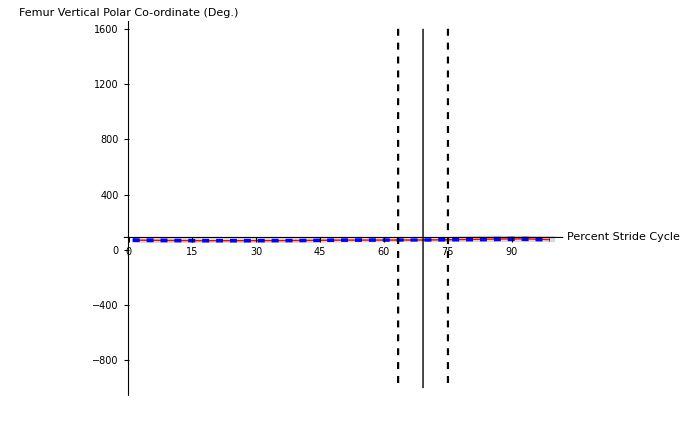

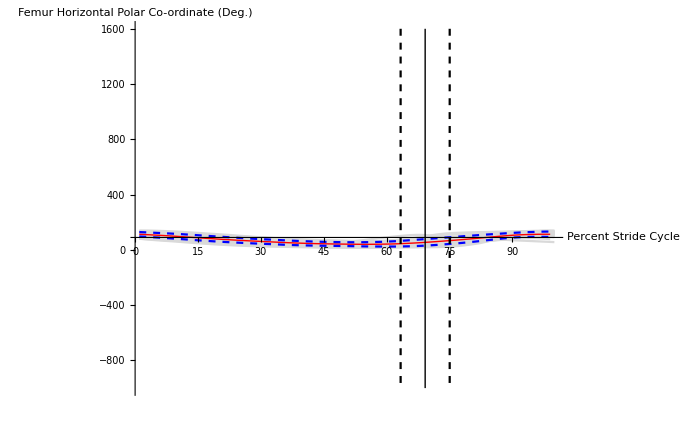

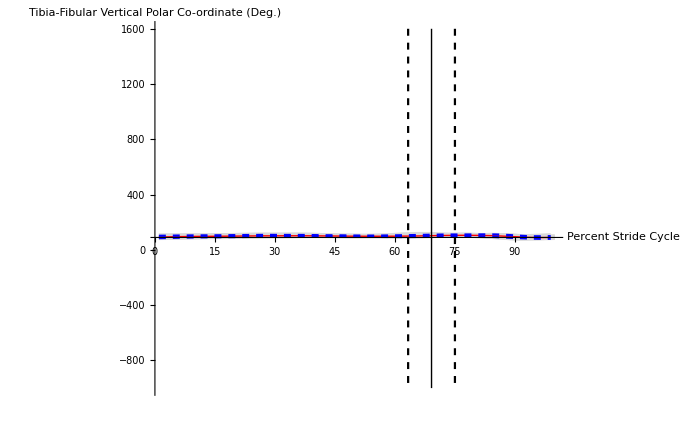

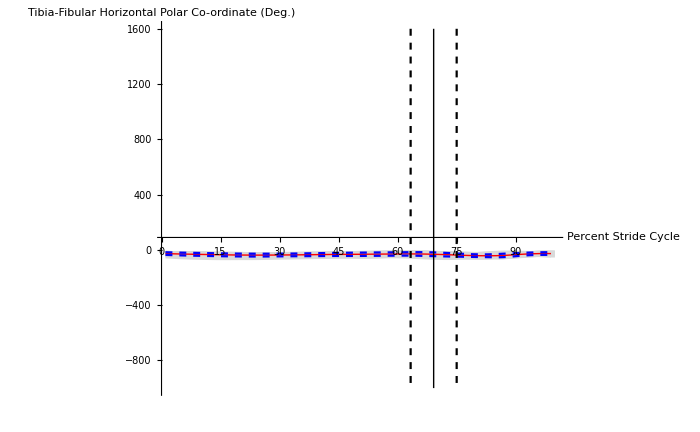

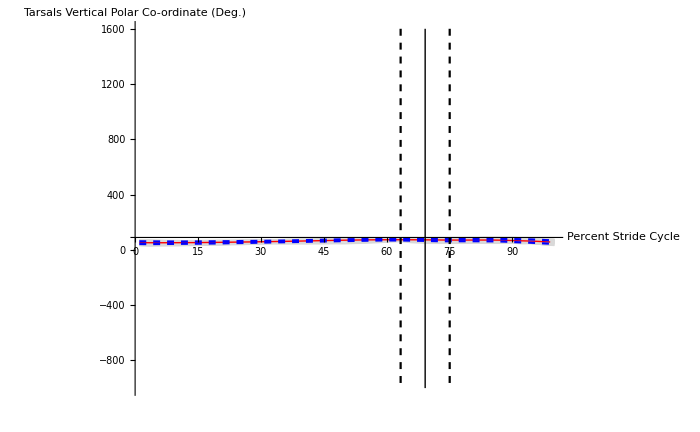

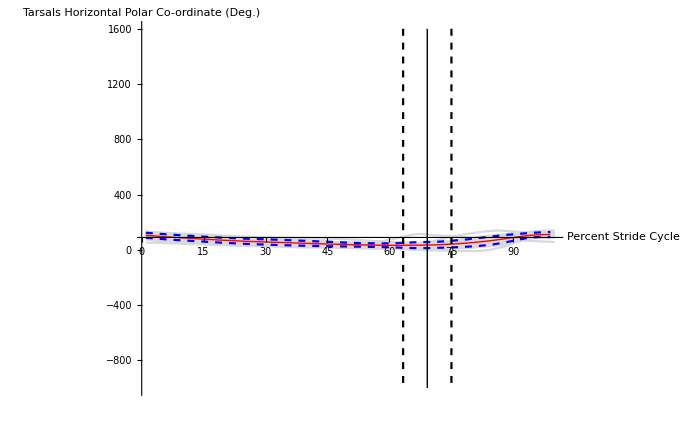

```mathematica
AllFEMV=Show[MeanSDFEMVPlot,MeanSDPSCStartofSwingPlot]

AllFEMH=Show[MeanSDFEMHPlot,MeanSDPSCStartofSwingPlot]


AllTIBV=Show[MeanSDTIBVPlot,MeanSDPSCStartofSwingPlot]

AllTIBH=Show[MeanSDTIBHPlot,MeanSDPSCStartofSwingPlot]


AllTARV=Show[MeanSDTARVPlot,MeanSDPSCStartofSwingPlot]

AllTARH=Show[MeanSDTARHPlot,MeanSDPSCStartofSwingPlot]
```

```mathematica
(*EXPORT*)
(*Export the images*)

dataDirectory="YOUR DIRECTORY FOR EXPORTED FIGURES";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export["Kinematics Paper - All Femur Vertical Polar Co-ordinates Plot.svg",AllFEMV];
Export["Kinematics Paper - All Femur Horizontal Polar Co-ordinates Plot.svg",AllFEMH];
Export["Kinematics Paper - All TibFib Vertical Polar Co-ordinates Plot.svg",AllTIBV];
Export["Kinematics Paper - All TibFib Horizontal Polar Co-ordinates Plot.svg",AllTIBH];
Export["Kinematics Paper - All Tarsals Vertical Polar Co-ordinates Plot.svg",AllTARV];
Export["Kinematics Paper - All Tarsals Horizontal Polar Co-ordinates Plot.svg",AllTARH];

Print["EXPORTED"]
```

EXPORTED

```mathematica
(*--- PLOTS FOR SI FIGURES----*)

(*organize data by frog partitions so individuals can be gathered.  But, skip first individual because it only has one trial*)

frogPartitions={{1},{2,3,4},{5,6,7},{8,9},{10,11,12,13,14},{15,16,17},{18,19},{20,21,22,23}};(*these are partitioned indices for each frog*)
frogPartitions=frogPartitions[[2;;]];

FEMVfrogmeans=Table[

trialData=AllRSTrialsFEMV[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
meanData=Map[Mean,trialData]
,{i,1,Length[frogPartitions]}];
FEMVfrogsds=Table[

trialData=AllRSTrialsFEMV[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
sdData=Map[StandardDeviation,trialData]
,{i,1,Length[frogPartitions]}];

FEMHfrogmeans=Table[

trialData=AllRSTrialsFEMH[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
meanData=Map[Mean,trialData]
,{i,1,Length[frogPartitions]}];
FEMHfrogsds=Table[

trialData=AllRSTrialsFEMH[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
sdData=Map[StandardDeviation,trialData]
,{i,1,Length[frogPartitions]}];

TIBVfrogmeans=Table[

trialData=AllRSTrialsTIBV[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
meanData=Map[Mean,trialData]
,{i,1,Length[frogPartitions]}];
TIBVfrogsds=Table[

trialData=AllRSTrialsTIBV[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
sdData=Map[StandardDeviation,trialData]
,{i,1,Length[frogPartitions]}];

TIBHfrogmeans=Table[

trialData=AllRSTrialsTIBH[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
meanData=Map[Mean,trialData]
,{i,1,Length[frogPartitions]}];
TIBHfrogsds=Table[

trialData=AllRSTrialsTIBH[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
sdData=Map[StandardDeviation,trialData]
,{i,1,Length[frogPartitions]}];

TARVfrogmeans=Table[

trialData=AllRSTrialsTARV[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
meanData=Map[Mean,trialData]
,{i,1,Length[frogPartitions]}];
TARVfrogsds=Table[

trialData=AllRSTrialsTARV[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
sdData=Map[StandardDeviation,trialData]
,{i,1,Length[frogPartitions]}];

TARHfrogmeans=Table[

trialData=AllRSTrialsTARH[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
meanData=Map[Mean,trialData]
,{i,1,Length[frogPartitions]}];
TARHfrogsds=Table[

trialData=AllRSTrialsTARH[[;;,frogPartitions[[i]]]];
Dimensions[trialData];
sdData=Map[StandardDeviation,trialData]
,{i,1,Length[frogPartitions]}];


(*----GENERATE PLOTS----*)


colors={(*Yellow,*)Red,Blue,Green,Cyan,Purple,Pink,Gray};
mDAT=FEMVfrogmeans;
sDAT=FEMVfrogsds;
FEMVrow=Table[
MEANindiv=ListLinePlot[mDAT[[i]],PlotStyle->colors[[i]],PlotRange->{{0,100},{50,100}}];
plusSDidiv=ListPlot[mDAT[[i]]+sDAT[[i]],PlotStyle->colors[[i]]];
minusSDidiv=ListPlot[mDAT[[i]]-sDAT[[i]],PlotStyle->colors[[i]]];
Show[MEANindiv,plusSDidiv,minusSDidiv,ImageSize->200],{i,1,Length[frogPartitions]}];

mDAT=FEMHfrogmeans;
sDAT=FEMHfrogsds;
FEMHrow=Table[
MEANindiv=ListLinePlot[mDAT[[i]],PlotStyle->colors[[i]],PlotRange->{{0,100},{0,150}}];
plusSDidiv=ListPlot[mDAT[[i]]+sDAT[[i]],PlotStyle->colors[[i]]];
minusSDidiv=ListPlot[mDAT[[i]]-sDAT[[i]],PlotStyle->colors[[i]]];
Show[MEANindiv,plusSDidiv,minusSDidiv,ImageSize->200],{i,1,Length[frogPartitions]}];

mDAT=TIBVfrogmeans;
sDAT=TIBVfrogsds;
TIBVrow=Table[
MEANindiv=ListLinePlot[mDAT[[i]],PlotStyle->colors[[i]],PlotRange->{{0,100},{50,150}}];
plusSDidiv=ListPlot[mDAT[[i]]+sDAT[[i]],PlotStyle->colors[[i]]];
minusSDidiv=ListPlot[mDAT[[i]]-sDAT[[i]],PlotStyle->colors[[i]]];
Show[MEANindiv,plusSDidiv,minusSDidiv,ImageSize->200],{i,1,Length[frogPartitions]}];

mDAT=TIBHfrogmeans;
sDAT=TIBHfrogsds;
TIBHrow=Table[
MEANindiv=ListLinePlot[mDAT[[i]],PlotStyle->colors[[i]],PlotRange->{{0,100},{-80,0}}];
plusSDidiv=ListPlot[mDAT[[i]]+sDAT[[i]],PlotStyle->colors[[i]]];
minusSDidiv=ListPlot[mDAT[[i]]-sDAT[[i]],PlotStyle->colors[[i]]];
Show[MEANindiv,plusSDidiv,minusSDidiv,ImageSize->200],{i,1,Length[frogPartitions]}];

mDAT=TARVfrogmeans;
sDAT=TARVfrogsds;
TARVrow=Table[
MEANindiv=ListLinePlot[mDAT[[i]],PlotStyle->colors[[i]],PlotRange->{{0,100},{0,100}}];
plusSDidiv=ListPlot[mDAT[[i]]+sDAT[[i]],PlotStyle->colors[[i]]];
minusSDidiv=ListPlot[mDAT[[i]]-sDAT[[i]],PlotStyle->colors[[i]]];
Show[MEANindiv,plusSDidiv,minusSDidiv,ImageSize->200],{i,1,Length[frogPartitions]}];

mDAT=TARHfrogmeans;
sDAT=TARHfrogsds;
TARHrow=Table[
MEANindiv=ListLinePlot[mDAT[[i]],PlotStyle->colors[[i]],PlotRange->{{0,100},{0,150}}];
plusSDidiv=ListPlot[mDAT[[i]]+sDAT[[i]],PlotStyle->colors[[i]]];
minusSDidiv=ListPlot[mDAT[[i]]-sDAT[[i]],PlotStyle->colors[[i]]];
Show[MEANindiv,plusSDidiv,minusSDidiv,ImageSize->200],{i,1,Length[frogPartitions]}];
polarPage1=GraphicsRow[{GraphicsColumn[FEMVrow,PlotLabel->"Femur Vertial\nPolar Co-ordinate (Deg)"],GraphicsColumn[FEMHrow,PlotLabel->"Femur Horizontal\nPolar Co-ordinate (Deg)"]}]
polarPage2=GraphicsRow[{GraphicsColumn[TIBVrow,PlotLabel->"Tibia-Fibular Vertial\nPolar Co-ordinate (Deg)"],GraphicsColumn[TIBHrow,PlotLabel->"Tibia-Fibular Horizontal\nPolar Co-ordinate (Deg)"]}]
polarPage3=GraphicsRow[{GraphicsColumn[TARVrow,PlotLabel->"Tarsals Vertial\nPolar Co-ordinate (Deg)"],GraphicsColumn[TARHrow,PlotLabel->"Tarsals Horizontal\nPolar Co-ordinate (Deg)"]}]

-Graphics-
-Graphics-
```

```mathematica
(*EXPORT*)
(*Export the images*)

dataDirectory="YOUR DIRECTORY FOR EXPORTED FIGURES";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export["SI_PolarCoordinatesByIndividual_page1.pdf",polarPage1];
Export["SI_PolarCoordinatesByIndividual_page2.pdf",polarPage2];
Export["SI_PolarCoordinatesByIndividual_page3.pdf",polarPage3];

Print["EXPORTED"]
```

EXPORTED